## Function Definitions (Run this Chapter)

## Defining Functions (Run this Section)

### General Functions

```mathematica
(*The function below is used to swap the position of two elements in a list. The user inputs a list and the two indices of elements to be swapped. The function returns the inputted list with requested elements swapped.*)
Swap[list_,element1_,element2_]:=Block[{newlist=list},{newlist[[element1]],newlist[[element2]]}={newlist[[element2]],newlist[[element1]]};
newlist];

NormalizeKet[columnVec_]:=Transpose[{Normalize[Flatten[Transpose[columnVec]]]}];

NormKet[TestState_]:=((TestState[[FirstPosition[Flatten[Transpose[TestState]],_?(##≠ 0&)][[1]]]][[1]])^(-1))*TestState;

NormBra[TestState_]:=((TestState[[FirstPosition[TestState,_?(##≠ 0&)][[1]]]])^(-1))*TestState;

NormMatrix[matrix_]:=((Numerator[matrix[[Sequence@@FirstPosition[matrix,_?(##≠ 0&)]]]])^(-1))*matrix;

(*Here we define functions related to calculating entanglement entropy for quantum systems.*)
(*The function below builds the density matrix for a given quantum state by taking the outer product of the state ket with its corresponding bra. The user inputs the ket representing the chosen system and the function will return the corresponding density matrix.*)
DensityMatrix[state_]:= state.ConjugateTranspose[state];

(*The following function builds the state ket from a density matrix. The user inputs a density matrix describing a quantum state, and the function returns the ket representation of that state.*)
KetProjector[ρ_]:=Module[{stateket={},basisbra = {ConstantArray[0,Dimensions[ρ][[1]]]},indexlist = Range[Dimensions[ρ][[1]]],i,j},For[i=1,i<Length[indexlist]+1,i++,AppendTo[stateket,{Sqrt[Flatten[ReplacePart[basisbra,{1,i}-> 1].ρ.Transpose[ReplacePart[basisbra,{1,i}-> 1]]][[1]]]}]];stateket];

GenerateVacuumKet[dim_]:=ReplacePart[ConstantArray[{0},2^dim],1->{1}];

(*The function below is used to construct a modified density matrix corresponding to a permutation of qubits. The user inputs the dimension of the system along with an indexed list displaying the desired new ordering of qubits. The function will generate and return the desired change of basis matrix. *)
PermutedIdentity[dim_,NewOrderList_]:= Module[{OriginalList = Tuples[{0,1},dim],PermutedPiece,PermutedList={},NewIdentity = IdentityMatrix[2^dim],i,j,k},For[i=1,i< (2^dim) +1,i++,PermutedPiece = {};
For[k=1,k<Length[NewOrderList]+1,k++,AppendTo[PermutedPiece,OriginalList[[i]][[-NewOrderList[[-k]]]]]];AppendTo[PermutedList,PermutedPiece]];
If[Max[NewOrderList] ≤ dim,For[j=1 ,j<(2^dim) +1,j++,NewIdentity = Swap[NewIdentity,j,Position[PermutedList,OriginalList[[j]]][[1,1]]];PermutedList = Swap[PermutedList,j,Position[PermutedList,OriginalList[[j]]][[1,1]]]],Print["Invalid qubit number."],Print["Unable to interpret qubit number."]];
NewIdentity];

tupFunc[n_]:=Tuples[{0,1},n]

FastPermutedIdentity[dim_,NewOrderList_,matrixDim_]:=Block[{OriginalList=tupFunc[dim],pos,NewIdentity=IdentityMatrix[matrixDim],PermutedList},

PermutedList=OriginalList[[All,-Reverse[NewOrderList]]];

Table[pos = Position[PermutedList,OriginalList[[j]]][[1,1]];
NewIdentity = Swap[NewIdentity,j,pos];
PermutedList = Swap[PermutedList,j,pos],{j,matrixDim}];
NewIdentity];

(*OldFastPermutedIdentity[dim_,NewOrderList_,matrixDim_]:= Block[{OriginalList = Tuples[{0,1},dim],pos,NewIdentity=IdentityMatrix[matrixDim],PermutedList},

PermutedList=Table[OriginalList[[i]][[-NewOrderList[[-k]]]],{i,matrixDim},{k,dim}];

Table[pos = First[First[Position[PermutedList,OriginalList[[j]]]]];
NewIdentity = Swap[NewIdentity,j,pos];
PermutedList = Swap[PermutedList,j,pos],{j,matrixDim}];
NewIdentity];*)

(*The GroupGenerate[] function generates a finite group of operators given a set of generators in a matrix representation.*)
GroupGenerate[generators_,parallelQ_]:=Block[{g = Join[{IdentityMatrix[First[Dimensions[First[generators]]]]},generators],count=0,newElements=1},
count=Length[g];

If[parallelQ==True,
While[newElements>0,
g = DeleteDuplicates[Flatten[ParallelTable[g[[i]].g[[j]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
],
While[newElements>0,
g = DeleteDuplicates[Flatten[Table[g[[i]].g[[j]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
]];
g]

NormedGroupGenerate[generators_,parallelQ_]:=Block[{g = Join[{IdentityMatrix[First[Dimensions[First[generators]]]]},generators],count=0,newElements=1},
count=Length[g];

If[parallelQ==True,
While[newElements>0,
g = DeleteDuplicates[Flatten[ParallelTable[NormKet[g[[i]].g[[j]]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
],
While[newElements>0,
g = DeleteDuplicates[Flatten[Table[NormKet[g[[i]].g[[j]]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
]];
g]
```

### Quantum Entropy Functions

#### Old Density Reduced Density Functions

```mathematica
(*(*Here we use the code for computing partial trace from Mark S.Tame.The program is run by calling
TraceSystem[DensityMatrix,{SubsystemIndex1,SubsystemIndex2,...}].The first argument of the function is the original density matrix to be reduced.There is an assumed ordering of elements of your density matrix, consider the two-qubit example below:{{Basis, <00|, <01|, <10|, <11|}, {|00>, a, b, c, d}, {|01>, e, f, g, h}, {|10>, i, j, k, l}, {|11>, m, n, o, p}}                           
 Subscript[ρ, sys]=({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})Subsystem indexing follows that of the constituent qubits,beginning at index 1. For exampleTraceSystem[DensityMatrix,{1}]would return the reduced density matrix given by tracing out over the first qubit.*)


(*Program below. The user inputs the density matrix to be traced out, along with the indices of substates that will be traced over.*)
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];
]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]
];Return[TrkM])*)
```

#### Entanglement Entropy and Entropy Vector

```mathematica
(*Function to compute the reduced density matrix.*)
ReducedDensityMatrix[densityMatrix_,desiredSubsystem_]:=Block[{tracedQubits,conjDens,dimB,permId,id,r,systemSize=Log2[Length[densityMatrix]]},

tracedQubits=Complement[Range[systemSize],desiredSubsystem];
dimB=2^Length[tracedQubits];
permId=FastPermutedIdentity[systemSize,Join[desiredSubsystem,tracedQubits],2^systemSize];
conjDens = permId.densityMatrix.ConjugateTranspose[permId];
id=IdentityMatrix[2^Length[desiredSubsystem]];

Sum[(KroneckerProduct[{UnitVector[dimB,r]},id]).conjDens.(KroneckerProduct[Transpose[{UnitVector[dimB,r]}],id]),{r,1,dimB}]];

(*Function to compute the von Neumann entropy of a chosen subsystem of qubits.*)
NormalizeDensityMatrix[dens_]:=dens/Tr[dens];

SvonNeumannBinary[dens_,SubsystemList_]:= Block[{rdm,eigVals},rdm=ReducedDensityMatrix[NormalizeDensityMatrix[dens],SubsystemList];
eigVals=Select[Eigenvalues[rdm],#!=0&]; 
-Total[eigVals*Log2[eigVals]]];

SvonNeumannDec[dens_,SubsystemList_]:= Block[{NonzeroEigenlist},
NonzeroEigenlist = DeleteCases[Eigenvalues[ReducedDensityMatrix[NormalizeDensityMatrix[dens],SubsystemList]],0|0.];
-1*Total[Flatten[Table[NonzeroEigenlist[[i]]*Log[NonzeroEigenlist[[i]]],{i,Length[NonzeroEigenlist]}]]]];

(*Function to build the reduced entropy vector for a density matrix.*)
ReducedEntropyVectorBuilder[dens_]:=Block[{dims = Log[2,Length[dens]],SubSystemList},
SubSystemList = Drop[Delete[Subsets[Range[dims]],1],-((2^(dims)-1)+1)/2];
ParallelTable[{SvonNeumannBinary[dens,SubSystemList[[i]]]},{i,Length[SubSystemList]}]];

ReducedEntropyVectors[StateSet_]:= Table[ReducedEntropyVectorBuilder[DensityMatrix[StateSet[[k]]]],{k,Length[StateSet]}];

(*Below is a function to construct the entropy vector for a system using the above vonNeumann entropy function applied to each subsystem. The user inputs the ket representing the full state and the function returns the entropy vector.*)
EntropyVectorBuilder[dens_]:=Block[{reducedEntropy = ReducedEntropyVectorBuilder[dens]},Join[reducedEntropy,Reverse[reducedEntropy],{{0}}]]

GenericEntropyVectorBuilder[dens_]:=Block[{dims = Log[2,Length[dens]],SubSystemList},
SubSystemList = Delete[Subsets[Range[dims]],1];
ParallelTable[{SvonNeumannBinary[dens,SubSystemList[[i]]]},{i,Length[SubSystemList]}]];

(*Below is a function that inputs a set of states and returns a list of entropy vectors corresponding to each state in the set.*)
EntropyVectors[StateSet_]:= Table[EntropyVectorBuilder[StateSet[[k]]],{k,Length[StateSet]}];
```

```mathematica
(*(*Function to compute the von Neumann entropy of a chosen subsystem of qubits.*)
SvonNeumannBinary[StateKet_,SubsystemList_]:= Block[{NonzeroEigenlist,NormKet = Transpose[{Normalize[First[Transpose[StateKet]]]}]},
NonzeroEigenlist = DeleteCases[Eigenvalues[TraceSystem[DensityMatrix[NormKet],Delete[Reverse[Range[Log[2,Length[StateKet]]]],Transpose[{SubsystemList}]]]],0];
-1*Total[Flatten[Table[NonzeroEigenlist[[i]]*Log[2,NonzeroEigenlist[[i]]],{i,Length[NonzeroEigenlist]}]]]];

(*Function to build the reduced entropy vector for a state.*)
ReducedEntropyVectorBuilder[StateKet_]:=Block[{dims = Log[2,Length[StateKet]],SubSystemList},
SubSystemList = Drop[Delete[Subsets[Range[dims]],1],-((2^(dims)-1)+1)/2];
ParallelTable[{SvonNeumannBinary[StateKet,SubSystemList[[i]]]},{i,Length[SubSystemList]}]];

(*Function to build the reduced entropy vector for a set of states.*)
ReducedEntropyVectors[StateSet_]:= Table[ReducedEntropyVectorBuilder[StateSet[[k]]],{k,Length[StateSet]}];

(*Below is a function to construct the entropy vector for a system using the above vonNeumann entropy function applied to each subsystem. The user inputs the ket representing the full state and the function returns the entropy vector.*)
EntropyVectorBuilder[StateKet_]:=Block[{reducedEntropy = ReducedEntropyVectorBuilder[StateKet]},Join[reducedEntropy,Reverse[reducedEntropy],{{0}}]]

(*Below is a function that inputs a set of states and returns a list of entropy vectors corresponding to each state in the set.*)
EntropyVectors[StateSet_]:= Table[EntropyVectorBuilder[StateSet[[k]]],{k,Length[StateSet]}];*)
```

#### Entropy Measures and Inequalities

```mathematica
(*Here we wish to build functions that evaluate whether an entropy vector satisfies certain entropy inequalities.*)
```

```mathematica
(*Subadditivity states: S(A)+S(B)≥ S(AB)*)
SubadditivityChecker[EntropyVector_]:=Module[{Dim = Log[2,Length[EntropyVector]-1]+1},];
```

```mathematica
(*Strong Subadditivity states: S(AB)+S(BC)≥ S(B)+S(ABC)*)
StrongSubadditivityChecker[EntropyVector_]:=Module[{Dim = Log[2,Length[EntropyVector]-1]+1},];
```

```mathematica
(*MMI states: S(AB)+S(AC)+S(BC)≥ S(A)+S(B)+S(C)+S(ABC)
More generally stated: Let I(A:B)=S(A)+S(B)-S(AB), then I(A:BC)≥ I(A:B)+I(A:C).*)
MutualInformationFunction[StateKet_,RegionA_,RegionB_]:= Module[{MutualInformationMeasure},
MutualInformationMeasure = SvonNeumannBinary[StateKet,RegionA] + SvonNeumannBinary[StateKet,RegionB] - SvonNeumannBinary[StateKet,DeleteDuplicates[Join[RegionA,RegionB]]];
MutualInformationMeasure]

MMICheckerEntropyInput[FullEntropyVector_]:=Block[{EVecTranspose = Flatten[Transpose[FullEntropyVector]],EVecIndices = DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}],PossibleTriples = Subsets[DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]],3],{}],{3}],DisjointTriples = {},evalutationTable = {}},

DisjointTriples = DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];


evalutationTable = Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]== EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];

evalutationTable
(*If[MemberQ[evalutationTable,False],False,True,Print["Cannot interpret."]]*)
]
```

```mathematica
(*Ingleton states: Let S(X|Y) = S(XY)-S(Y), then I(A:B|C)+I(A:B|D)+I(C:D)≥ I(A:B)*)
IngletonCheckerEntropyInput[FullEntropyVector_,DisjointQuads_,TFboolean_]:=
Block[{EVecIndices = DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}],evalutationTable = {}},

If[TFboolean==True,
evalutationTable = ParallelTable[If[(FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]]]]][[1,1]]]] +FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,4]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,2]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,2]],DisjointQuads[[k,4]]]]][[1,1]]]])[[1]]== 
(FullEntropyVector[[Position[EVecIndices,Sort[DisjointQuads[[k,1]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[DisjointQuads[[k,2]]]][[1,1]]]]
+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]],DisjointQuads[[k,4]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,3]],DisjointQuads[[k,4]]]]][[1,1]]]])[[1]],"Saturates",If[(FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]]]]][[1,1]]]] +FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,4]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,2]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,2]],DisjointQuads[[k,4]]]]][[1,1]]]])[[1]]> 
(FullEntropyVector[[Position[EVecIndices,Sort[DisjointQuads[[k,1]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[DisjointQuads[[k,2]]]][[1,1]]]]
+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]],DisjointQuads[[k,4]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,3]],DisjointQuads[[k,4]]]]][[1,1]]]])[[1]],"Satisfies","Fails"]],{k,Length[DisjointQuads]}];,
evalutationTable = Table[If[(FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]]]]][[1,1]]]] +FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,4]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,2]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,2]],DisjointQuads[[k,4]]]]][[1,1]]]])[[1]]== 
(FullEntropyVector[[Position[EVecIndices,Sort[DisjointQuads[[k,1]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[DisjointQuads[[k,2]]]][[1,1]]]]
+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]],DisjointQuads[[k,4]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,3]],DisjointQuads[[k,4]]]]][[1,1]]]])[[1]],"Saturates",If[(FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]]]]][[1,1]]]] +FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,4]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,2]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,2]],DisjointQuads[[k,4]]]]][[1,1]]]])[[1]]> 
(FullEntropyVector[[Position[EVecIndices,Sort[DisjointQuads[[k,1]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[DisjointQuads[[k,2]]]][[1,1]]]]
+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]],DisjointQuads[[k,3]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,1]],DisjointQuads[[k,2]],DisjointQuads[[k,4]]]]][[1,1]]]]+FullEntropyVector[[Position[EVecIndices,Sort[Union[DisjointQuads[[k,3]],DisjointQuads[[k,4]]]]][[1,1]]]])[[1]],"Satisfies","Fails"]],{k,Length[DisjointQuads]}];];
evalutationTable]
```

#### Holographic Considerations

```mathematica
(*Below we define a function to determine whether a state's entropy vector satisfies the necessary conditions to be a holographic state, and thus whether it lives within the holographic entropy cone. The user inputs a ket and the function returns a boolean True or False.*)
HolographicChecker[StateVector_]:=Module[{SubsystemCount = Log[2,Length[Flatten[StateVector]]],EntropyVec = Flatten[EntropyVectorBuilder[StateVector]],Result=False},

(*There are no entangled single-party states, and all systems with sub-party number below 3 are holographic.*)
If[SubsystemCount<3,Result=True,

(*Verify the 3-party entropy inequalities (Strong Subadditivity and MMI) are satisfied.*)
If[SubsystemCount == 3,Result = And[EntropyVec[[4]]+EntropyVec[[6]]≥ EntropyVec[[2]]+EntropyVec[[7]],EntropyVec[[4]]+EntropyVec[[5]]≥ EntropyVec[[3]]+EntropyVec[[7]],EntropyVec[[5]]+EntropyVec[[6]]≥ EntropyVec[[1]]+EntropyVec[[7]],EntropyVec[[4]]+EntropyVec[[5]]+EntropyVec[[6]]≥ EntropyVec[[1]]+EntropyVec[[2]]+EntropyVec[[3]]+EntropyVec[[7]]],

(*Verify the 4-party entropy inequalities are satisfied.*)
If[SubsystemCount == 4,Result =False,Print["Subsystem count too high."]]]];
Result]
```

```mathematica
InequalityPermuter[InitialInstance_,SingleQubitSubsystems_]:=Block[{singleQPermutations = Permutations[SingleQubitSubsystems],initialOrder,initialPositions,allPermutations},
initialOrder = First[singleQPermutations];
Print[initialOrder];
initialPositions = Table[Table[Position[initialOrder,InitialInstance[[i,j]]],{j,Length[InitialInstance[[i]]]}],{i,Length[InitialInstance]}];
Print[initialPositions];
allPermutations=Table[Sort/@Table[Table[singleQPermutations[[k]][[Flatten[initialPositions[[i,j]]]]],{j,Length[initialPositions[[i]]]}],{i,Length[initialPositions]}],{k,Length[singleQPermutations]}];
allPermutations]

EntropyInequalityChecker[FullEntropyVector_,InstancePermutations_,LHS_]:=Block[{regions = DeleteCases[Subsets[Join[{"A","B","C","D","E","F","G","H","I"}[[;;(Log[2,Length[FullEntropyVector]+1])-1]],{"O"}],(Log[2,Length[FullEntropyVector]+1])],{}],ineqLength = Length[First[InstancePermutations]],evalutationTable = {}},
evalutationTable = Table[If[Total[Table[FullEntropyVector[[First[Position[regions,Flatten[InstancePermutations[[i,j]]]]]]],{j,1,LHS}]][[1,1]]== Total[Table[FullEntropyVector[[First[Position[regions,Flatten[InstancePermutations[[i,j]]]]]]],{j,LHS+1,ineqLength}]][[1,1]],"Saturates",If[Total[Table[FullEntropyVector[[First[Position[regions,Flatten[InstancePermutations[[i,j]]]]]]],{j,1,LHS}]][[1,1]]>= Total[Table[FullEntropyVector[[First[Position[regions,Flatten[InstancePermutations[[i,j]]]]]]],{j,LHS+1,ineqLength}]][[1,1]],"Satisfies","Fails"]],{i,Length[InstancePermutations]}];
evalutationTable]
```

### Defining Quantum Logic Gates

```mathematica
(*Here we define functions to reproduce the effects of various quantum logic gates on a quantum system or subsystem.*)
```

#### For Internal Use

```mathematica
(*Below is a function to reproduce the Hadamard gate acting on a single qubit of a multiqubit system. The user inputs the ket representing the state of the system, along with the index of the qubit to be acted on with the Hadamard gate. The function returns an updated ket for the full system.*)
HadamardGate[StateKet_,AffectedQubit_]:=Module[{FinalState,PermIdentity,BaseHMatrix = HadamardMatrix[2],OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]],i++,BaseHMatrix = KroneckerProduct[IdentityMatrix[2],BaseHMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Swap[OriginalOrder,1,AffectedQubit]];
FinalState = ConjugateTranspose[PermIdentity].(BaseHMatrix.(PermIdentity.StateKet));
FinalState];

(*Here is the same Hadamard gate without the normalization factor.*)
NonNormHadamardGate[StateKet_,AffectedQubit_]:=Module[{},NonNormHadamardAction[Log[2,Length[StateKet]],AffectedQubit].StateKet];

NormalizedHadamardGate[StateKet_,AffectedQubit_]:=Module[{},Transpose[{Normalize[Flatten[Transpose[NonNormHadamardAction[Log[2,Length[StateKet]],AffectedQubit].StateKet]]]}]];

NonNormHadamardAction[Dimension_,AffectedQubit_]:=Module[{PermIdentity,BaseHMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],Sqrt[2]*HadamardMatrix[2]],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseHMatrix.PermIdentity];

(*Below is a function to convert a qubit from one basis into some unequal superposition of a different basis.*)
UnequalHadamardGate[StateKet_,AffectedQubit_,Probability1_]:=Module[{FinalState,PermIdentity,BaseHMatrix = {{Sqrt[Probability1],Sqrt[1-Probability1]},{Sqrt[1-Probability1],-Sqrt[Probability1]}},OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]],i++,BaseHMatrix = KroneckerProduct[IdentityMatrix[2],BaseHMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Swap[OriginalOrder,1,AffectedQubit]];
FinalState = ConjugateTranspose[PermIdentity].(BaseHMatrix.(PermIdentity.StateKet));
FinalState];

(*Below is a function to represent the CNOT gate. The user must input the state ket for the system, the index of the control qubit, and the index of the target qubit. Input format is CNOT[StateKet,#control,#target]. The function will return the updated state ket for the system.*)
CNOTGate[StateKet_,controlbitnumber_,targetbitnumber_]:= Module[{FinalState,PermIdentity,BaseCNOTMatrix = {{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}},OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]]-1,i++,BaseCNOTMatrix = KroneckerProduct[IdentityMatrix[2],BaseCNOTMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Join[{controlbitnumber,targetbitnumber},Delete[OriginalOrder,{{controlbitnumber},{targetbitnumber}}]]];
FinalState = ConjugateTranspose[PermIdentity].(BaseCNOTMatrix.(PermIdentity.StateKet));
FinalState];

(*Entered [ket,{c,t}]*)
CNOTAction[Dimension_,CTpair_]:=Module[{FinalState,PermIdentity,BaseCNOTMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCNOTMatrix.PermIdentity];

(*Below is a function to reproduce the Phase gate. The user must input the state ket for the system, followed by the index of the qubit upon which the Phase gate will act. The function will return the updated ket for the full system.*)
PhaseGate[StateKet_,AffectedQubit_]:=Module[{},PhaseAction[Log[2,Length[StateKet]],AffectedQubit].StateKet];

PhaseAction[Dimension_,AffectedQubit_]:=Module[{PermIdentity,BasePMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,I}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BasePMatrix.PermIdentity];


(*Below is a function to reproduce the Controlled Phase Gate. The user must input the state ket for the system, followed by the indices of the control qubit and target qubit, in that order. The function will return the updated ket after this applied operation.*)
ControlledPhaseGate[StateKet_,controlbitnumber_,targetbitnumber_]:= Module[{FinalState,PermIdentity,BaseCNOTMatrix = {{1,0,0,0},{0,0,1,0},{0,0,0,-1},{0,1,0,0}},OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]]-1,i++,BaseCNOTMatrix = KroneckerProduct[IdentityMatrix[2],BaseCNOTMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Join[{controlbitnumber,targetbitnumber},Delete[OriginalOrder,{{controlbitnumber},{targetbitnumber}}]]];
FinalState = ConjugateTranspose[PermIdentity].(BaseCNOTMatrix.(PermIdentity.StateKet));
FinalState];

XGate[StateKet_,AffectedQubit_]:=Module[{},XAction[Log[2,Length[StateKet]],AffectedQubit].StateKet];

XAction[Dimension_,AffectedQubit_]:=Module[{PermIdentity,BaseXMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{0,1},{1,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseXMatrix.PermIdentity];

CliffordGenerators[Dimension_]:=Block[{ntuples = Tuples[Range[Dimension],{2}]},Join[Table[NonNormHadamardAction[Dimension,i],{i,Dimension}],Table[PhaseAction[Dimension,i],{i,Dimension}],DeleteCases[Table[If[ntuples[[j,1]]≠ ntuples[[j,2]],CNOTAction[Dimension,ntuples[[j]]],Null],{j,Length[ntuples]}],Null]]];



(*To include the W-state we need to include the R_y gate that makes 1/n rotations and the controlled-H gate.*)
YRotationGate[StateKet_,Angle_,AffectedQubit_]:=Module[{},YRotationAction[Log[2,Length[StateKet]],Angle,AffectedQubit].StateKet]

YRotationAction[Dimension_,Angle_,AffectedQubit_]:=Module[{PermIdentity,BaseRYMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{Cos[Angle/2],-Sin[Angle/2]},{Sin[Angle/2],Cos[Angle/2]}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseRYMatrix.PermIdentity];

CHGate[StateKet_,controlbitnumber_,targetbitnumber_]:= Module[{FinalState,PermIdentity,BaseCHMatrix = {{1,0,0,0},{0,1,0,0},{0,0,1/Sqrt[2],1/Sqrt[2]},{0,0,1/Sqrt[2],-1/Sqrt[2]}},OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]]-1,i++,BaseCHMatrix = KroneckerProduct[IdentityMatrix[2],BaseCHMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Join[{controlbitnumber,targetbitnumber},Delete[OriginalOrder,{{controlbitnumber},{targetbitnumber}}]]];
FinalState = ConjugateTranspose[PermIdentity].(BaseCHMatrix.(PermIdentity.StateKet));
FinalState];

(*Entered [ket,{c,t}]*)
CHAction[Dimension_,CTpair_]:=Module[{FinalState,PermIdentity,BaseCHMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,1,0,0},{0,0,1/Sqrt[2],1/Sqrt[2]},{0,0,1/Sqrt[2],-1/Sqrt[2]}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCHMatrix.PermIdentity];
```

#### For User

```mathematica
HadamardGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity},
PermIdentity = PermutedIdentity[Dimension,Swap[Range[Dimension],1,AffectedQubit]];
ConjugateTranspose[PermIdentity].KroneckerProduct[IdentityMatrix[2^(Dimension-1)],HadamardMatrix[2]].PermIdentity];

UnequalHadamardGate[Dimension_,AffectedQubit_,Probability1_]:=Block[{PermIdentity},
PermIdentity = PermutedIdentity[Dimension,Swap[Range[Dimension],1,AffectedQubit]];
ConjugateTranspose[PermIdentity].KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{Sqrt[Probability1],Sqrt[1-Probability1]},{Sqrt[1-Probability1],-Sqrt[Probability1]}}].PermIdentity];

PhaseGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity},
PermIdentity = PermutedIdentity[Dimension,Swap[Range[Dimension],1,AffectedQubit]];
ConjugateTranspose[PermIdentity].KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,I}}].PermIdentity];

TGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity},
PermIdentity = PermutedIdentity[Dimension,Swap[Range[Dimension],1,AffectedQubit]];
ConjugateTranspose[PermIdentity].KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,Exp[I*Pi/4]}}].PermIdentity];

CNOTGate[Dimension_,CTpair_]:=Block[{FinalState,PermIdentity,BaseCNOTMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCNOTMatrix.PermIdentity];

XGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity,BaseXMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{0,1},{1,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseXMatrix.PermIdentity];

YGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity,BaseYMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{0,-I},{I,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseYMatrix.PermIdentity];

ZGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity,BaseZMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,-1}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseZMatrix.PermIdentity];

IdentityGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity,BaseIMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,1}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseIMatrix.PermIdentity];

CHGate[Dimension_,CTpair_]:=Block[{FinalState,PermIdentity,BaseCHMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,1/Sqrt[2],0,1/Sqrt[2]},{0,0,1,0},{0,1/Sqrt[2],0,-1/Sqrt[2]}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCHMatrix.PermIdentity];

CPhaseGate[Dimension_,CTpair_]:=Block[{FinalState,PermIdentity,BaseCPMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,I}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCPMatrix.PermIdentity];

CZGate[Dimension_,CTpair_]:=Block[{FinalState,PermIdentity,BaseCHMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCHMatrix.PermIdentity];

CRotYGate[Dimension_,Angle_,CTpair_]:=Block[{FinalState,PermIdentity,BaseCHMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,1,0,0},{0,0,Cos[Angle/2],-Sin[Angle/2]},{0,0,Sin[Angle/2],Cos[Angle/2]}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCHMatrix.PermIdentity];

CliffordGenerators[Dimension_]:=Block[{ntuples = Tuples[Range[Dimension],{2}]},Join[Table[HadamardGate[Dimension,i],{i,Dimension}],Table[PhaseGate[Dimension,i],{i,Dimension}],DeleteCases[Table[If[ntuples[[j,1]]≠ ntuples[[j,2]],CNOTGate[Dimension,ntuples[[j]]],Null],{j,Length[ntuples]}],Null]]];

CCXGate[Dimension_,CCTtriple_]:=CNOTGate[Dimension,CCTtriple[[;;2]]].HadamardGate[Dimension,Last[CCTtriple]].Inverse[TGate[Dimension,CCTtriple[[2]]]].TGate[Dimension,CCTtriple[[1]]].TGate[Dimension,Last[CCTtriple]].CNOTGate[Dimension,CCTtriple[[;;2]]].CNOTGate[Dimension,CCTtriple[[{1,3}]]].TGate[Dimension,CCTtriple[[2]]].Inverse[TGate[Dimension,Last[CCTtriple]]].CNOTGate[Dimension,CCTtriple[[2;;]]].TGate[Dimension,Last[CCTtriple]].CNOTGate[Dimension,CCTtriple[[{1,3}]]].Inverse[TGate[Dimension,Last[CCTtriple]]].CNOTGate[Dimension,CCTtriple[[2;;]]].HadamardGate[Dimension,Last[CCTtriple]];
```

```mathematica
{1,2,7}[[{1,3}]]
```

{1,7}

```mathematica
TGate[3,2]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^((ⅈ π)/4) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^((ⅈ π)/4) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ π)/4) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ π)/4))

```mathematica
Timing[Inverse[TGate[6,2]]]
```

{0.056507,{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(ⅈ π)/4)}}}

### Defining Quantum Circuits

```mathematica
(*Here we wish to define a set of functions that ma be used to evaluate entire quantum circuits.*)
```

```mathematica
(*The function below models a complete stabilizer circuit. The user inputs the ket representing the initial state of the system, followed by a list of operations to be performed, followed by the corresponding list of qubits upon which each gate will act. The function will output the entropy vector for the system after each operation, and return the final updated system ket at the end. A sample input to this function would be StabilizerCircuit[ϕ,{HadamardGate,HadamardGate,CNOTGate},{{1},{2},{2,3}}].*)
StabilizerCircuit[StateKet_,OperationsList_,QubitList_]:= Module[{UpdatedKet = StateKet,i,t},For[t=1,t<Length[OperationsList]+1,t++,If[OperationsList[[t]]== CNOTGate,UpdatedKet = OperationsList[[t]][UpdatedKet,QubitList[[t,1]],QubitList[[t,2]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]]];
Print["At time t= ",t," the system is in the state ",UpdatedKet//MatrixForm, " with entropy vector ",EntropyVectorBuilder[UpdatedKet]//MatrixForm]];
UpdatedKet];

(*Below is a function that computes a full stabilizer circuit, returning only the updated state vector at the end.*)
StabilizerCircuitOnlyVector[StateKet_,OperationsList_,QubitList_]:= Module[{UpdatedKet = StateKet,i,t},For[t=1,t<Length[OperationsList]+1,t++,If[OperationsList[[t]]== CNOTGate,UpdatedKet = OperationsList[[t]][UpdatedKet,QubitList[[t,1]],QubitList[[t,2]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]]]];
((UpdatedKet[[FirstPosition[Flatten[Transpose[UpdatedKet]],_?(##≠ 0&)][[1]]]][[1]])^(-1))*UpdatedKet];

(*The following is used when defining graph paths through a sequence of operations on a particular stabilizer state. The user inputs the ket for the initial state, the ordered list of operations, the associated list of respective qubits to be operated upon, and the overall stabilizer state set to which the states belong.*)
StabilizerCircuitIndices[StateKet_,OperationsList_,QubitList_,StabilizerStateSet_]:= Module[{UpdatedKet = StateKet,IndexSet = {Position[StabilizerStateSet,StateKet]},i,t},
For[t=1,t<Length[OperationsList]+1,t++,
If[OperationsList[[t]]== CNOTGate,
UpdatedKet = OperationsList[[t]][UpdatedKet,QubitList[[t,1]],QubitList[[t,2]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]]];
AppendTo[IndexSet,Position[StabilizerStateSet,((UpdatedKet[[FirstPosition[Flatten[Transpose[UpdatedKet]],_?(##≠ 0&)][[1]]]][[1]])^(-1))*UpdatedKet]]];
Flatten[IndexSet]];

(*Below is a function to produce the set of generators for a given stabilizer state. At this point, the user must input the inital state ket and the stabilizer circuit used to build the chosen state from the initial state.*)
GeneratorSetVacuum[Dimensions_,OperationsList_,QubitList_ ]:=Module[{InitialTable={},StabilizerSet={},i ,j,k},For[i=1,i<(Dimensions+1),i++,AppendTo[InitialTable,ReplacePart[ConstantArray[0,2*Dimensions],(Dimensions+i)-> 1]]];
For[j=1,j< (Length[OperationsList]+1),j++,If[TrueQ[OperationsList[[j]]== HadamardGate],InitialTable[[All,{QubitList[[j,1]],Dimensions+QubitList[[j,1]]}]] = InitialTable[[All,{Dimensions+QubitList[[j,1]],QubitList[[j,1]]}]],
If[TrueQ[OperationsList[[j]]== CNOTGate],InitialTable[[All,QubitList[[j,2]]]]=BitXor[InitialTable[[All,QubitList[[j,1]]]],InitialTable[[All,QubitList[[j,2]]]]];InitialTable[[All,Dimensions + QubitList[[j,1]]]]=BitXor[InitialTable[[All,Dimensions+QubitList[[j,2]]]],InitialTable[[All,Dimensions + QubitList[[j,1]]]]],
If[TrueQ[OperationsList[[j]]== PhaseGate],InitialTable[[All,Dimensions + QubitList[[j,1]]]]=BitXor[InitialTable[[All,QubitList[[j,1]]]],InitialTable[[All,Dimensions+QubitList[[j,1]]]]]]]]];
Print[InitialTable//MatrixForm];
For[k=1,k<(Dimensions+1),k++,AppendTo[StabilizerSet,Replace[Replace[InitialTable[[k]],1->PauliMatrix[3],{1} ],0-> IdentityMatrix[2],{1}][[Dimensions+1;;2*Dimensions]]]];
Print["Generating set is ", StabilizerSet]];
```

### Stabilizer State Functions

We construct a function to generate all stabilizer states for a given qubit number. The user inputs the number of qubits and the function procedurally generates the set of all stabilizer states for that qubit number, beginning from the n-qubit vacuum state.

```mathematica
StabilizerStateSetGenerator[Dimension_]:=Block[{PredictedCount = ((2^Dimension)*Product[(2^num)+1,{num,1,Dimension}]),UpdatedStabilizerStateSet={ReplacePart[ConstantArray[{0},2^Dimension],1->{1}]},CheckSet={ReplacePart[ConstantArray[{0},2^Dimension],1->{1}]},TotalGateSet=CliffordGenerators[Dimension]},

While[Length[UpdatedStabilizerStateSet]<PredictedCount,

CheckSet = DeleteDuplicates[Flatten[Table[NormKet[TotalGateSet[[k]].CheckSet[[l]]],{k,Length[TotalGateSet]},{l,Length[CheckSet]}],1]];

UpdatedStabilizerStateSet = DeleteDuplicates[Join[UpdatedStabilizerStateSet,CheckSet]];
Print[Length[UpdatedStabilizerStateSet]];
];
UpdatedStabilizerStateSet]
```

```mathematica
SelectiveStabilizerGenerator[IntialState_,GateSet_,DesiredNumberOfStates_]:=Block[{UpdatedStabilizerStateSet={IntialState},CheckSet={IntialState},StatesChecked={}},

While[And[SubsetQ[StatesChecked,CheckSet]== False,Length[UpdatedStabilizerStateSet]<DesiredNumberOfStates],
StatesChecked = UpdatedStabilizerStateSet;
CheckSet = DeleteDuplicates[Flatten[Table[NormKet[GateSet[[k]].CheckSet[[l]]],{k,Length[GateSet]},{l,Length[CheckSet]}],1]];

UpdatedStabilizerStateSet = DeleteDuplicates[Join[UpdatedStabilizerStateSet,CheckSet]];
];
DeleteDuplicates[UpdatedStabilizerStateSet]]
```

The function below compiles all stabilizer states, as with the one above, but tracks (up to one gate operation) how the state was reached. In essence, this function stores information about all states, how each can be reached from its (2n + Permutation[n,2]) neighboring states, as well as the entropy vector of the state. The output is organized as follows (Final State, Gate Applied, Qubit Acted Upon, Initial State, Entropy Vector of Final State). The user inputs the set of stabilizer states to be considered. The output is an array of (2n + Permutation[n,2])(2^n Prod[(2^k + 1),{k,1,n}]) elements.

```mathematica
(*Input desired gates as strings.*)
SelectiveStateWithGateGenerator[StateSet_,DesiredGates_]:=Block[{dimension = Log[2,Length[StateSet[[1]]]],selectedGates={},StatesWithGates = {},i},

For[i=1,i<Length[DesiredGates]+1,i++,
If[DesiredGates[[i,1]]== "H",AppendTo[selectedGates,{DesiredGates[[i]],NonNormHadamardAction[dimension,DesiredGates[[i,2,1]]]}],
If[DesiredGates[[i,1]]== "P",AppendTo[selectedGates,{DesiredGates[[i]],PhaseAction[dimension,DesiredGates[[i,2,1]]]}],
If[DesiredGates[[i,1]]== "CNOT",AppendTo[selectedGates,{DesiredGates[[i]],CNOTAction[dimension,DesiredGates[[i,2]]]}],Print["Non-Clifford Gate Encountered."]]]];];

Print["Gates Compiled."];

Flatten[Table[{NormKet[selectedGates[[j,2]].StateSet[[i]]],selectedGates[[j,1]],StateSet[[i]],ReducedEntropyVectorBuilder[NormKet[selectedGates[[j,2]].StateSet[[i]]]]},{i,Length[StateSet]},{j,Length[selectedGates]}],1]
]
```

```mathematica
(*Input desired gates as strings.*)
```

### Dicke State Functions

```mathematica
DickeState[n_,k_]:=Block[{base=ConstantArray[{{1},{0}},n],positions = Subsets[Range[n],{k}],replacements,states,final},
replacements = Table[positions[[i,j]]->{{0},{1}},{i,Length[positions]},{j,k}];
states = Table[ReplacePart[base,replacements[[l]]],{l,Length[replacements]}];
final = Total[Table[KroneckerProduct@@states[[m]],{m,Length[states]}]];
1/(Sqrt[Binomial[n,k]])*final]
```

### “Random” State Functions

```mathematica
SelectiveRandomStateGenerator[IntialState_,GateSet_,DesiredNumberOfStates_,Precision_]:=Block[{UpdatedStabilizerStateSet={IntialState},CheckSet={IntialState},StatesChecked={}},

While[And[SubsetQ[StatesChecked,CheckSet]== False,Length[UpdatedStabilizerStateSet]<DesiredNumberOfStates],
StatesChecked = UpdatedStabilizerStateSet;
CheckSet = DeleteDuplicatesBy[Flatten[Table[NormKet[GateSet[[k]].CheckSet[[l]]],{k,Length[GateSet]},{l,Length[CheckSet]}],1],RealEquivalence];

UpdatedStabilizerStateSet = DeleteDuplicatesBy[Join[UpdatedStabilizerStateSet,CheckSet],RealEquivalence];
];
DeleteDuplicatesBy[UpdatedStabilizerStateSet,RealEquivalence]]
```

### Defining Visualization Functions

```mathematica
SimpleReachabilityGraphBuilder[SetofStates_,SetOfStatesWithGates_,GatesToBeDisplayed_]:=Module[{PossibleEntropyVectorList,OperationsConsidered = {},TestValue,EdgeSet={},VertexStyleSet = {},
EntropyColorChoices = {Red,Blue,Orange,Purple,Yellow,Black,Cyan,Pink,Brown,LightGreen,White,LightRed,LightBlue,LightYellow,LightMagenta,LightOrange,LightGray,LightCyan,LightBrown},i,j,k=0,m,G},

For[i=1,i<Length[GatesToBeDisplayed]+1,i++,OperationsConsidered = Join[OperationsConsidered,Position[SetOfStatesWithGates,GatesToBeDisplayed[[i]]]]];

If[Log[2,Length[SetofStates[[1]]]]>4,

(*For[m=1,m< Length[SetofStates]+1,m++,

AppendTo[VertexLabelSet,m-> Placed[Toggler[Invisible[m],{Style[ToString[Flatten[Transpose[SetOfStabilizerStates[[m]]]]],{Background-> LightYellow,CellFrameColor-> LightBlue,CellFrame-> 1}],Style[ToString[ReducedEntropyVectorBuilder[SetOfStabilizerStates[[m]]]],{Background-> LightBlue,CellFrameColor-> LightBlue,CellFrame-> 1}],Invisible[m]}],Center]]]*)Null,
PossibleEntropyVectorList = DeleteDuplicates[ReducedEntropyVectors[SetofStates]];
For[m=1,m< Length[SetofStates]+1,m++,
AppendTo[VertexStyleSet ,{m}->EntropyColorChoices[[Position[PossibleEntropyVectorList,ReducedEntropyVectorBuilder[SetofStates[[m]]]][[1]]]][[1]]]]];

For[j=1,j<Length[OperationsConsidered]+1,j++,
TestValue = SetOfStatesWithGates[[OperationsConsidered[[j]][[1]]]];

If[TestValue[[2,1]]=="P" ,AppendTo[EdgeSet,DirectedEdge[Position[SetofStates,TestValue[[3]]][[1]],Position[SetofStates,TestValue[[1]]][[1]]]],
If[TestValue[[2,1]]=="H" ,AppendTo[EdgeSet,Style[Sort[Position[SetofStates,TestValue[[3]]][[1]]<-> Position[SetofStates,TestValue[[1]]][[1]]],Green]],
AppendTo[EdgeSet,Style[Sort[Position[SetofStates,TestValue[[3]]][[1]]<-> Position[SetofStates,TestValue[[1]]][[1]]],Magenta]],Print["Invalid Gate Encountered."]],Print["Cannot determine gate input."]];

k++;

If[k>1000,Print[j," of ",Length[OperationsConsidered]," edges added."];k=0,Null]];

(*Uses the edge set compiled above to render the graph.*)
If[Log[2,Length[SetofStates[[1]]]]>4,G = Graph[EdgeSet],
G = Graph[EdgeSet,VertexStyle->VertexStyleSet]];
G]
```

```mathematica
GraphFinder[StateSet_,GateSet_,DesiredVertexNumber_]:=Module[{TestGraph,RandomizedSequence = RandomSample[StateSet],i},
For[i=1,i<Length[RandomizedSequence]+1,i++,
TestGraph =SimpleGraph[GateSelectedStateGenerator[RandomizedSequence[[i]],GateSet]];
If[VertexCount[TestGraph]== DesiredVertexNumber,Print[TestGraph];Print[RandomizedSequence[[i]]],Print["Graph: ",i,", Vertex Number: ",VertexCount[TestGraph]];Print[RandomizedSequence[[i]]]]]
]
```

```mathematica
InteractiveReachabilityGraphBuilder[SetOfStabilizerStates_,SetOfStatesWithGates_,GatesToBeDisplayed_]:=Module[{NumberOfQubits = Log[2,Length[SetOfStabilizerStates[[1]]]],PossibleEntropyVectors = DeleteDuplicates[ReducedEntropyVectors[SetOfStabilizerStates]],GateBitPair={},HolographicStates = {},OperationIndices,EdgeSet={},VertexLabelSet={},VertexStyleSet = {},
VertexColorChoices = {Red,Blue,Orange,Purple,Yellow,Black,Cyan,Pink,Brown,LightGreen,White,LightRed,LightBlue,LightYellow,LightMagenta,LightOrange,LightGray,LightCyan,LightBrown},i,j,k,l,m,G},

If[Log[2,Length[SetOfStabilizerStates[[1]]]]>4,

For[m=1,m< Length[SetOfStabilizerStates]+1,m++,
AppendTo[VertexLabelSet,m-> Placed[Toggler[Invisible[m],{Style[ToString[Flatten[Transpose[SetOfStabilizerStates[[m]]]]],{Background-> LightYellow,CellFrameColor-> LightBlue,CellFrame-> 1}],Style[ToString[ReducedEntropyVectorBuilder[SetOfStabilizerStates[[m]]]],{Background-> LightBlue,CellFrameColor-> LightBlue,CellFrame-> 1}],Invisible[m]}],Center]]],

For[m=1,m< Length[SetOfStabilizerStates]+1,m++,
AppendTo[VertexLabelSet,m-> Placed[Toggler[Invisible[m],{Style[ToString[Flatten[Transpose[SetOfStabilizerStates[[m]]]]],{Background-> LightYellow,CellFrameColor-> LightBlue,CellFrame-> 1}],Style[ToString[ReducedEntropyVectorBuilder[SetOfStabilizerStates[[m]]]],{Background-> LightBlue,CellFrameColor-> LightBlue,CellFrame-> 1}],Invisible[m]}],Center]];AppendTo[VertexStyleSet ,m->VertexColorChoices[[Position[PossibleEntropyVectors,ReducedEntropyVectorBuilder[SetOfStabilizerStates[[m]]]][[1]]]][[1]]]]];

(*For the user's sanity*)
Print["Vertices colored and labeled."];

For[j=1,j<Length[SetOfStatesWithGates]+1,j++,AppendTo[GateBitPair,{ToString[SetOfStatesWithGates[[j,2]]],SetOfStatesWithGates[[j,3]]}]];
(*For the user's sanity*)
Print["Gates compiled."];

For[l=1,l< Length[GatesToBeDisplayed]+1,l++,
OperationIndices = Position[GateBitPair,GatesToBeDisplayed[[l]]];
For[k=1,k<Length[OperationIndices]+1,k++,
If[GatesToBeDisplayed[[l,1]]=="P" ,AppendTo[EdgeSet,DirectedEdge[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]]],If[GatesToBeDisplayed[[l,1]]=="H" ,AppendTo[EdgeSet,Style[Min[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]]<-> Max[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]],Blend[{Green,White},1-1/(SetOfStatesWithGates[[OperationIndices[[k,1]],3,1]])]]],AppendTo[EdgeSet,Style[Min[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]]<-> Max[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]],Blend[{Magenta,White},1-1/(SetOfStatesWithGates[[OperationIndices[[k,1]],3,1]])]]],Print["Unknown Operation."]]]];

(*For the user's sanity*)
Print["Edge set ",ToString[l]," of ",ToString[Length[GatesToBeDisplayed]], " added."]];

(*Uses the edge set compiled above to render the graph.*)
If[Log[2,Length[SetOfStabilizerStates[[1]]]]>4,G = Graph[DeleteDuplicates[EdgeSet],VertexLabels->VertexLabelSet],
G = Graph[DeleteDuplicates[EdgeSet],VertexLabels->VertexLabelSet,VertexStyle-> VertexStyleSet]];
G]
```

```mathematica
(*Below we define a function to generate the reachability graph for any number of qubits.*)
(*Input: ImprovedReachabilityGraphBuilder[ThreeQubitStatesWithGates,{{"H",{3}},{"CNOT",{2,1}},{"P"{1}}}*)

ReachabilityGraphBuilder[StatesWithGates_,DesiredGates_]:=Block[{EdgeList={},entropyVectors,EdgeStyleList = {Dashing[{}],Dashing[{Small}],Dashing[{Tiny}],Dashing[{Medium}],Dashing[{Large}]},VStyleList={},VertexColorChoices = {Blue,Red,Orange,Purple,Yellow,Black,Cyan,Pink,Brown,LightGreen,White,LightRed,LightBlue,LightYellow,LightMagenta,LightOrange,LightGray,LightCyan,LightBrown},currentEntry,j,LoopCounter=0,chosenIndices},

chosenIndices = Flatten[Table[Most/@Position[StatesWithGates,DesiredGates[[i]]],{i,Length[DesiredGates]}]];

entropyVectors = Sort[DeleteDuplicates[Table[StatesWithGates[[chosenIndices[[j]],4]],{j,Length[chosenIndices]}]]];

For[j = 1,j<Length[chosenIndices]+1,j++,
currentEntry = StatesWithGates[[chosenIndices[[j]]]];
AppendTo[VStyleList,currentEntry[[1]]->VertexColorChoices[[First[Position[entropyVectors,currentEntry[[4]]]]]]];
If[currentEntry[[2,1]]=="P" ,AppendTo[EdgeList,Style[DirectedEdge[currentEntry[[3]],currentEntry[[1]]],{EdgeStyleList[[currentEntry[[2,2,1]]]]}]],
If[currentEntry[[2,1]]=="H",AppendTo[EdgeList,Style[Sort[currentEntry[[3]]<-> currentEntry[[1]]],{Green,EdgeStyleList[[currentEntry[[2,2,1]]]]}]],AppendTo[EdgeList,Style[Sort[currentEntry[[3]]<-> currentEntry[[1]]],{Magenta,EdgeStyleList[[currentEntry[[2,2,1]]]]}]]]];

LoopCounter++;
(*For user sanity.*)
If[LoopCounter>1000,Print[j," of ",Length[chosenIndices]," edges added."];LoopCounter=0,Null];
];

Print["Entropy Vector Legend:"];
Print[Table[{VertexColorChoices[[First[Position[entropyVectors,entropyVectors[[k]]]]]],entropyVectors[[k]]},{k,Length[entropyVectors]}]//MatrixForm];

Graph[EdgeList,VertexStyle-> VStyleList,EdgeStyle->EdgeStyleList]
]
```

```mathematica
(*Below is a function to find and display all cycles of a chosen length, containing the chosen bit-address as a vertex. The user inputs the graph they are examining, the bit-address of the vertex to be included, the chosen length of the cycle, and the number corresponding to which of the found cycles should be displayed. This function is meant to be used in conjunction with the slider feature.*)
CycleFinder[InitialGraph_,StartingBitAddress_,CycleLength_,ChosenCycleNumber_]:=Module[{StateSet,ChosenCycle,CycleList,SortedCycleList,NumCycles,i,j},
If[Log[2,Length[StartingBitAddress]] == 1,StateSet = OneQubitStabilizerStates,If[Log[2,Length[StartingBitAddress]] == 2,StateSet = TwoQubitStabilizerStates,If[Log[2,Length[StartingBitAddress]] == 3,StateSet = ThreeQubitStabilizerStates,
If[Log[2,Length[StartingBitAddress]] == 4,StateSet = FourQubitStabilizerStates,
If[Log[2,Length[StartingBitAddress]] == 5,StateSet = FiveQubitStabilizerStates,Print["Invalid bit-address."],Print["Unable to interpret bit-address"]]]]]];
CycleList = FindCycle[{InitialGraph,Position[StateSet,Transpose[{StartingBitAddress}]][[1,1]]},{CycleLength},All];
NumCycles = Length[CycleList];
Print["There are ",NumCycles," cycles of length ", CycleLength, " involving ", StartingBitAddress, "." ];
For[i=1,i< Length[CycleList]+1,i++,
For[j=1,j<CycleLength+1,j++,CycleList[[i,j]]= Sort[CycleList[[i,j]]]]];
Print["Displaying cycle ",ChosenCycleNumber,":"];
HighlightGraph[InitialGraph,Style[CycleList[[ChosenCycleNumber]],Thick,Black]]]
```

```mathematica
(*Below is a function to generate all classes of subgraph corresponding to a particular graph. The user inputs a chosen graph along with a boolean value indicating whether all subgraphs should be displayed or not. The generator produces all subgraphs and categorizes them according to vertex number, displaying nondegenrate examples of each if requested.*)
ConnectedSubgraphGenerator[InitialGraph_,DisplaySubgraphBoolean_]:=Module[{UpdatedVertexList,SubgraphSet={},DropList={},VertexCountList={},VertexNumList={},SubgraphVertexList={},i,j,k,g,h},

UpdatedVertexList = VertexList[InitialGraph];
While[Length[UpdatedVertexList]>0,AppendTo[SubgraphSet,Flatten[ConnectedComponents[InitialGraph,UpdatedVertexList[[1]]]]];
UpdatedVertexList = DeleteCases[UpdatedVertexList,Alternatives@@Intersection[UpdatedVertexList,Flatten[ConnectedComponents[InitialGraph,UpdatedVertexList[[1]]]]]]];
For[i=1,i<Length[SubgraphSet]+1,i++,AppendTo[VertexCountList,Length[SubgraphSet[[i]]]]];
VertexNumList=DeleteDuplicates[VertexCountList];
Print["There are ",Length[SubgraphSet], " separate, connected subgraphs of vertex numbers ",VertexNumList ,"."];
For[j=1,j<Length[VertexNumList]+1,j++,Print["There are ",Count[VertexCountList,VertexNumList[[j]]]," connected subgraphs of ",VertexNumList[[j]]," vertices."]];

If[DisplaySubgraphBoolean== True,
For[g=1,g<Length[SubgraphSet]+1,g++,
For[h=1,h<Length[SubgraphSet]+1,h++,If[And[g≠ h,IsomorphicGraphQ[Subgraph[InitialGraph,ConnectedComponents[InitialGraph,SubgraphSet[[g]]]],Subgraph[InitialGraph,ConnectedComponents[InitialGraph,SubgraphSet[[h]]]]]],AppendTo[DropList,{h}],Null,Print["Cannot determine if isomorphic."]
]];SubgraphSet = Delete[SubgraphSet,DropList];DropList={}];For[k=1,k<Length[SubgraphSet]+1,k++,Print[Subgraph[InitialGraph,ConnectedComponents[InitialGraph,SubgraphSet[[k]]]]]],Null]
]
```

```mathematica
SequenceGenerator[InitialGraph_,GraphPath_,SetOfStates_,SetOfStatesWithEntropy_]:=Module[{FlattenedPath = Flatten[GraphPath],SequenceOfGates = {},SequenceOfQubits ={},SequenceOfOperations,PairsList={},i,j},
For[i=1,i<Length[FlattenedPath],i++,AppendTo[PairsList,First[Position[SetOfStatesWithEntropy,{SetOfStates[[FlattenedPath[[i+1]]]],_,_, SetOfStates[[FlattenedPath[[i]]]],_}]]]];
For[j=1,j<Length[Flatten[PairsList]]+1,j++,AppendTo[SequenceOfGates,SetOfStatesWithEntropy[[Flatten[PairsList][[j]]]][[2]]];AppendTo[SequenceOfQubits,SetOfStatesWithEntropy[[Flatten[PairsList][[j]]]][[3]]]];
SequenceOfOperations = {ReplaceAll[SequenceOfGates,{"H"-> HadamardGate,"CNOT"-> CNOTGate,"P"-> PhaseGate}],SequenceOfQubits};
SequenceOfOperations]
```

```mathematica
HolographicStateFinder[InitialGraph_,StabilizerStateSet_]:=Module[{HolographicVertices={},i},For[i=1,i<Length[VertexList[InitialGraph]]+1,i++,If[HolographicChecker[StabilizerStateSet[[i]]]== True,AppendTo[HolographicVertices,i],Null]];
HighlightGraph[InitialGraph,Style[HolographicVertices,Large,Green]]]
```

```mathematica
(*Below we define a set of functions to help visualize entropy vector manipulation. This is limited to dimensions = 3.*)
EntropyVectorVisualize3D[EntropyVector_]:=Graphics3D[{InfiniteLine[{0,0,0},{1,0,0}],InfiniteLine[{0,0,0},{0,1,0}],InfiniteLine[{0,0,0},{0,0,1}],Red,Thick,InfiniteLine[{0,0,0},{EntropyVector[[1,1]],EntropyVector[[2,1]],EntropyVector[[3,1]]}]},PlotRange->{{0,10},{0,10},{0,10}}];
```

```mathematica
EntropyConeVisualize3D[EntropyVector_]:=Graphics3D[{InfiniteLine[{0,0,0},{1,0,0}],InfiniteLine[{0,0,0},{0,1,0}],InfiniteLine[{0,0,0},{0,0,1}],Polygon[{{0,0,0},{1,1,0},{0,1,0},{0,0,1}}]},PlotRange->{{0,10},{0,10},{0,10}}];
```

```mathematica
UnitCellGenerator[IntialState_]:=Block[{dim = Log[2,Length[IntialState]],UnitCycle,StateSet={},StatesWithGates = {},FullGraph},
UnitCycle = {NonNormHadamardAction[dim, 1],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 1],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],NonNormHadamardAction[dim, 1],NonNormHadamardAction[dim, 2],NonNormHadamardAction[dim, 1],NonNormHadamardAction[dim, 2],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}]};

StateSet = SelectiveStabilizerGenerator[IntialState,{NonNormHadamardAction[dim,1],NonNormHadamardAction[dim,2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}]},100];
StatesWithGates=SelectiveStateWithGateGenerator[StateSet,{{"H",{1}},{"H",{2}},{"CNOT",{1,2}},{"CNOT",{2,1}}}];
FullGraph = ReachabilityGraphBuilder[StatesWithGates,{{"H",{1}},{"H",{2}},{"CNOT",{1,2}},{"CNOT",{2,1}}}];
SimpleGraph[Subgraph[FullGraph,Table[NormKet[Apply[Dot,Reverse[UnitCycle[[1;;i]]]].IntialState],{i,Length[UnitCycle]}]]]]


DualCellGenerator[IntialState_]:=Block[{dim = Log[2,Length[IntialState]],UnitCycle,StateSet={},StatesWithGates = {},FullGraph},
UnitCycle = {NonNormHadamardAction[dim, 1],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 1],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],NonNormHadamardAction[dim, 1],NonNormHadamardAction[dim, 2],NonNormHadamardAction[dim, 1],NonNormHadamardAction[dim, 2],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}]};

StateSet = SelectiveStabilizerGenerator[IntialState,{NonNormHadamardAction[dim,1],NonNormHadamardAction[dim,2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}]},100];
StatesWithGates=SelectiveStateWithGateGenerator[StateSet,{{"H",{1}},{"H",{2}},{"CNOT",{1,2}},{"CNOT",{2,1}}}];
FullGraph = ReachabilityGraphBuilder[StatesWithGates,{{"H",{1}},{"H",{2}},{"CNOT",{1,2}},{"CNOT",{2,1}}}];
SimpleGraph[Subgraph[FullGraph,Table[NormKet[Apply[Dot,UnitCycle[[1;;i]]].IntialState],{i,Length[UnitCycle]}]]]]
```

### Contracted Graph Functions

```mathematica
ContractedGraphBuilder[StatesWithGates_,DesiredGates_,ContractedOperations_]:=Block[{EdgeGates = DeleteCases[DesiredGates,Alternatives@@ContractedOperations],initialGraph,annotationStyle,annotatedPositions,contractedIndices,vReplacements={},contractedStyles={},contractedGraph,contractedEdges={1},counter=1},

initialGraph = SimpleGraph[ReachabilityGraphBuilder[StatesWithGates,DesiredGates]];
Print[initialGraph];
contractedGraph = initialGraph;
annotationStyle = AnnotationValue[initialGraph,EdgeStyle];

contractedIndices = Sort[Flatten[Table[Most/@Position[StatesWithGates,ContractedOperations[[i]]],{i,Length[ContractedOperations]}]]];

annotatedPositions = Flatten[Most/@Flatten[DeleteDuplicates[DeleteCases[Join[Table[Position[annotationStyle,UndirectedEdge[StatesWithGates[[contractedIndices[[j]],3]],StatesWithGates[[contractedIndices[[j]],1]]]],{j,Length[contractedIndices]}],
Table[Position[annotationStyle,UndirectedEdge[StatesWithGates[[contractedIndices[[j]],1]],StatesWithGates[[contractedIndices[[j]],3]]]],{j,Length[contractedIndices]}]
],{}]],1]];

contractedStyles = DeleteDuplicates[Flatten[Table[annotationStyle[[annotatedPositions[[k]],2]],{k,Length[annotatedPositions]}],1]];

While[And[Length[contractedEdges]>0,counter<25],

contractedEdges = Join[Flatten[Table[EdgeList[contractedGraph,_?(AnnotationValue[{contractedGraph,#},EdgeStyle]=={contractedStyles[[l]]}&)],{l,Length[contractedStyles]}],1]];

vReplacements = Join[Flatten[Table[contractedEdges[[k,1]]->contractedEdges[[k,2]] ,{k,Length[contractedEdges]}],1]];

contractedGraph = SimpleGraph[VertexReplace[contractedGraph,vReplacements]];
Print[Length[contractedEdges]];
counter++;
];
contractedGraph
]
```

```mathematica
GraphContracter[Graph_,IdentifyingOperations_]:=Block[{vContraction={},vList = VertexList[Graph],edgeList=EdgeList[Graph],contractedGraph = Graph,contractedEdges={1},replacements,counter=1},
vContraction=Table[NormKet[IdentifyingOperations[[j]].vList[[i]]],{i,Length[vList]},{j,Length[IdentifyingOperations]}];

replacements = Flatten[Table[Table[vContraction[[i,j]]->First[vContraction[[i]]],{j,Length[vContraction[[i]]]}],{i,Length[vContraction]}],1];

contractedGraph= VertexReplace[Graph,replacements];
Print[Length[DeleteDuplicates[VertexList[contractedGraph]]]];
contractedGraph
]

(*GraphContracter[Graph_,TagsOfContractedOps_]:=Block[{vReplacements={},edges = EdgeList[Graph],tags = EdgeTags[Graph],contractedGraph = Graph,contractedEdges={1},replacements,counter=1},

contractedEdges = Table[edges[[Flatten[Position[tags,TagsOfContractedOps[[i]]]]]],{i,Length[TagsOfContractedOps]}];

While[And[Length[contractedEdges]>0,counter<5],
contractedEdges = Join[Flatten[ParallelTable[EdgeList[contractedGraph][[Flatten[Position[tags,TagsOfContractedOps[[i]]]]]],{i,Length[TagsOfContractedOps]}],1]];

replacements = Table[contractedEdges[[j,2]]->contractedEdges[[j,1]] ,{j,Length[contractedEdges]}];

Table[contractedGraph = VertexReplace[contractedGraph,replacements[[m]]],{m,Length[replacements]}];
Print[Length[contractedEdges]];
counter++;
];
removeSelfLoops@contractedGraph
]*)
```

```mathematica
ReducedGraphBuilder[StatesWithGates_,DesiredGates_,IdentifyingOperation_]:=Block[{initialGraph,vertices,vReplacements={},reducedGraph},

initialGraph = SimpleGraph[ReachabilityGraphBuilder[StatesWithGates,DesiredGates]];
Print[initialGraph];
vertices = VertexList[initialGraph];

vReplacements = Flatten[Table[{vertices [[i]]->NormKet[IdentifyingOperation.(vertices [[i]])]} ,{i,Length[vertices]}],1];
Print[Length[vReplacements]];
Print[Length[DeleteDuplicates[Sort/@vReplacements]]];
reducedGraph = SimpleGraph[VertexReplace[initialGraph,DeleteDuplicates[Sort/@vReplacements]]];

reducedGraph
]
```

```mathematica
EntropyDistance[Graph_,VertexColorList_]:=Block[{vColors =VertexColorList ,vSets = Table[VertexList[Graph,_?(AnnotationValue[{Graph,#},VertexStyle]=={VertexColorList[[i]]}&)],{i,Length[VertexColorList]}],distanceMatrix = {}},distanceMatrix=Table[If[j!=k,Min[Table[GraphDistance[Graph,vSets[[j,l]],vSets[[k,m]]],{l,Length[vSets[[j]]]},{m,Length[vSets[[k]]]}]],0],{j,Length[vSets]},{k,Length[vSets]}];
distanceMatrix = Transpose[PrependTo[distanceMatrix,vColors]];
PrependTo[distanceMatrix,PrependTo[vColors,"\\"]]]
```

### Cayley Graph Functions

```mathematica
ColorData[3,"ColorList"]

removeSelfLoops=EdgeDelete[#,(UndirectedEdge|DirectedEdge)[a_,a_,___]]&;

removeRedundantEdges[graph_]:=Block[{edgeStyle =AnnotationValue[graph,EdgeStyle] },
EdgeDelete[graph,(UndirectedEdge|DirectedEdge)[a_,b_,___]]&];

CayleyGraphBuilder[generators_]:=Block[{colors =ColorData[3,"ColorList"], edgeSet ,g ,vertexCount = 0,vList},

(*edgeSet =Flatten[Table[Style[DirectedEdge[generators[[i]],generators[[j]].generators[[i]],j],colors[[j]]],{i,Length[generators]},{j,Length[generators]}],1];*)
edgeSet =Flatten[Table[Style[DirectedEdge[generators[[i]],generators[[j]].generators[[i]],j],colors[[j]]],{i,Length[generators]},{j,Length[generators]}],1];
g = Graph[edgeSet];


While[VertexCount[g]>vertexCount,
vList = VertexList[g];
vertexCount = Length[vList];
edgeSet = DeleteDuplicates[Join[edgeSet,Flatten[ParallelTable[Style[DirectedEdge[vList[[i]],generators[[j]].vList[[i]],j],colors[[j]]],{i,Length[vList]},{j,Length[generators]}],1]]];
g = Graph[edgeSet]];
Graph[edgeSet]]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}

```mathematica
SimpleCayleyGraphBuilder[generators_]:=Block[{ edgeSet ,g ,vertexCount = 0,vList},

edgeSet =Flatten[Table[DirectedEdge[generators[[i]],generators[[j]].generators[[i]]],{i,Length[generators]},{j,Length[generators]}],1];
g = Graph[edgeSet];

While[VertexCount[g]>vertexCount,
vList = VertexList[g];
vertexCount = Length[vList];
edgeSet = DeleteDuplicates[Join[edgeSet,Flatten[ParallelTable[DirectedEdge[vList[[i]],generators[[j]].vList[[i]]],{i,Length[vList]},{j,Length[generators]}],1]]];
g = Graph[edgeSet]];
Graph[edgeSet]]
```

```mathematica
Congruence[x_,y_]:=Equal@@SetPrecision[{x,y},4]
```

```mathematica
CayleyGraphQuotient12[CayleyGraph_, State_]:=Block[{ops = VertexList[CayleyGraph],contractions,reachableStates, uniqueReachableStates,indices,edgeList = EdgeList[CayleyGraph],vertexContractions, indexGraph,indexGraphEdges},

reachableStates = Round[Table[NormKet[Round[ops[[i]],.0001].Round[State,.0001]],{i,Length[ops]}],.0001];

uniqueReachableStates = Gather[reachableStates,Congruence];

indices = Flatten/@ParallelTable[Table[Position[reachableStates,uniqueReachableStates[[i,j]]],{j,Length[uniqueReachableStates[[j]]]}],{i,Length[uniqueReachableStates]}];

(*FlipView[{CayleyGraph,Fold[VertexContract,CayleyGraph,contractions]}]*)

indexGraph = Graph[ParallelTable[DirectedEdge[VertexIndex[CayleyGraph,edgeList[[i,1]]],VertexIndex[CayleyGraph,edgeList[[i,2]]]],{i,Length[edgeList]}]];


SimpleGraph[VertexContract[indexGraph,indices]]
]
```

```mathematica
UniqueSubgraphFinder12[initialCayleyGraph_,num_]:=Block[{integerFactors = Divisors[VertexCount[initialCayleyGraph]],CayleyVertexList = VertexList[initialCayleyGraph],
eigenvectors ,actionTable,orbitLengthCount = {},uniqueSet,indices,contractions,graphTable},

If[num==0,
eigenvectors = Transpose/@ParallelTable[Eigenvectors[N[CayleyVertexList[[i]]],1],{i,Length[CayleyVertexList]}],
eigenvectors = Transpose/@ParallelTable[Eigenvectors[N[CayleyVertexList[[i]]],1],{i,num}]];
Print["Eigenvectors compiled."];
Print[integerFactors];

(*If[num==0,
graphTable = ParallelTable[{eigenvectors[[j]],
SimpleGraph[CayleyGraphQuotient[initialCayleyGraph, eigenvectors[[j]]]]},{j,Length[eigenvectors]}],
graphTable = ParallelTable[{eigenvectors[[j]],
SimpleGraph[CayleyGraphQuotient[initialCayleyGraph, eigenvectors[[j]]]]},{j,num}]];*)

graphTable = Table[
SimpleGraph[CayleyGraphQuotient12[initialCayleyGraph, eigenvectors[[j]]]],{j,Length[eigenvectors]}];
DeleteDuplicates[graphTable,IsomorphicGraphQ]
]
```

```mathematica
(*CayleyGraphQuotient13[CayleyGraph_, State_]:=Block[{ops = VertexList[CayleyGraph],reachableStates, uniqueReachableStates,indices},

reachableStates = Round[Table[NormKet[Round[ops[[i]],.0001].Round[State,.0001]],{i,Length[ops]}],.00001];

(*uniqueReachableStates = DeleteDuplicates[reachableStates,Congruence];*)
uniqueReachableStates = Gather[reachableStates,Congruence];

(*indices = Table[First/@Position[reachableStates,uniqueReachableStates[[i]]],{i,Length[uniqueReachableStates]}];*);
indices = DeleteDuplicates[Flatten[Table[Flatten[Position[reachableStates,uniqueReachableStates[[i,j]]]],{i,Length[uniqueReachableStates]},{j,Length[uniqueReachableStates[[i]]]}],1]];
(*FlipView[{CayleyGraph,Fold[VertexContract,CayleyGraph,contractions]}]*)

SimpleGraph[VertexContract[CayleyGraph,Table[ops[[indices[[k]]]],{k,Length[indices]}]]]
]*)

(*ImprovedCayleyGraphQuotient13[CayleyGraph_, State_]:=Block[{allOperations = VertexList[CayleyGraph],numericalGraph,numericalOperations,reachableStates,uniqueReachableStates,contractions,replacements,edgeList },

(*Convert all operators in the Cayley graphs to a numerical form for better comparison.*)
numericalGraph = EdgeTaggedGraph[VertexReplace[CayleyGraph,ParallelTable[allOperations[[i]]-> NormKet[allOperations[[i]]],{i,Length[allOperations]}]]];
numericalOperations = VertexList[numericalGraph];
edgeList = EdgeList[numericalGraph];
Print[EdgeTags[numericalGraph]];

(*Determine the sets of operators which take the target state to the same place, group these reachable states accordingly.*)
reachableStates = ParallelTable[NormKet[numericalOperations[[i]].State],{i,Length[numericalOperations]}];
uniqueReachableStates = Gather[reachableStates,Equal];

(*Locate all operations which led to the above groupings and group them identically.*)
contractions = ParallelTable[numericalOperations[[Flatten[Position[reachableStates,uniqueReachableStates[[k,1]]]]]],{k,Length[uniqueReachableStates]}];

(*Replace all operators of a grouping with the first element of that grouping.*)
replacements = Flatten[Table[contractions[[l,m]]-> First[contractions[[l]]],{l,Length[contractions]},{m,Length[contractions[[l]]]}],1];

SimpleGraph[VertexList[VertexReplace[numericalGraph,replacements]]]
(*removeSelfLoops@VertexReplace[numericalGraph,replacements]*)
]*)

CayleyGraphQuotient13[CayleyGraph_, State_]:=Block[{allOperations = VertexList[CayleyGraph],numericalGraph,numericalOperations,reachableStates,uniqueReachableStates,contractions,replacements,g },

(*Convert all operators in the Cayley graphs to a numerical form for better comparison.*)
numericalGraph = VertexReplace[CayleyGraph,ParallelTable[allOperations[[i]]-> NormKet[allOperations[[i]]],{i,Length[allOperations]}]];
numericalOperations = Sort[VertexList[numericalGraph]];

(*Determine the sets of operators which take the target state to the same place, group these reachable states accordingly.*)
reachableStates = ParallelTable[NormKet[numericalOperations[[i]].State],{i,Length[numericalOperations]}];
uniqueReachableStates = Gather[reachableStates,Equal];

(*Locate all operations which led to the above groupings and group them identically.*)
contractions = ParallelTable[numericalOperations[[Flatten[Position[reachableStates,uniqueReachableStates[[k,1]]]]]],{k,Length[uniqueReachableStates]}];
(*Replace all operators of a grouping with the first element of that grouping.*)
replacements = Flatten[Table[contractions[[l,m]]-> First[contractions[[l]]],{l,Length[contractions]},{m,Length[contractions[[l]]]}],1];

g=removeSelfLoops@VertexReplace[numericalGraph,replacements];
EdgeDelete[g,Flatten[Rest/@Gather[EdgeList[g], SameQ],1]]
]
```

```mathematica
UniqueSubgraphFinder13[initialCayleyGraph_,num_]:=Block[{integerFactors = Divisors[VertexCount[initialCayleyGraph]],CayleyVertexList = VertexList[initialCayleyGraph],
eigenvectors ,actionTable,orbitLengthCount = {},uniqueSet,indices,contractions,graphTable},

If[num==0,
eigenvectors = Transpose/@ParallelTable[Eigenvectors[N[CayleyVertexList[[i]]],1],{i,Length[CayleyVertexList]}],
eigenvectors = Transpose/@ParallelTable[Eigenvectors[N[CayleyVertexList[[i]]],1],{i,num}]];
Print["Eigenvectors compiled."];
Print[integerFactors];

graphTable = Table[
SimpleGraph[CayleyGraphQuotient13[initialCayleyGraph, eigenvectors[[j]]]],{j,Length[eigenvectors]}];
DeleteDuplicates[graphTable,IsomorphicGraphQ]
]


GlobalPhaseEquivalence[x_,y_]:=TrueQ[NormKet[x]== NormKet[y]];


GlobalPhaseQuotient12[CayleyGraph_]:=Block[{allOperations = VertexList[CayleyGraph],uniqueOperations,enumeratedGraph,enumeratedOps},

enumeratedGraph = VertexReplace[CayleyGraph,ParallelTable[allOperations[[i]]-> NormKet[allOperations[[i]]],{i,Length[allOperations]}]];
enumeratedOps = VertexList[enumeratedGraph];
Print["Vertices enumerated."];

uniqueOperations = Gather[enumeratedOps,Equal];
Print["Identical operations gathered."];

SimpleGraph[VertexContract[enumeratedGraph,uniqueOperations]]
]


GlobalPhaseQuotient13[CayleyGraph_]:=Block[{allOperations = VertexList[CayleyGraph],uniqueOperations,indices},

uniqueOperations = Gather[allOperations,GlobalPhaseEquivalence];

SimpleGraph[VertexContract[CayleyGraph,uniqueOperations]]
]
```

```mathematica
(*Use FlipView for a really cool display feature.*)
```

```mathematica
entropyVectorColors = {RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0.99, 0],RGBColor[0.996078431372549, 1, 0],RGBColor[1, 0, 1],RGBColor[0, 1, 1],RGBColor[0.7019607843137254, 0.7450980392156863, 0.8235294117647058],RGBColor[0, 0, 0],RGBColor[0.49, 0.49, 1],RGBColor[0, 0.49, 0.49],RGBColor[0.5, 1, 0.5]};

NormedGeneralGraphBuilder[states_,gateSet_,edgeStyleSet_]:=Block[{EdgeList={},dim=Log[2,Length[states[[1]]]],i,j,k},
Table[If[gateSet[[i]]==Inverse[gateSet[[i]]],
Table[AppendTo[EdgeList,Style[UndirectedEdge[states[[j]],NormKet[gateSet[[i]].states[[j]]]],edgeStyleSet[[i]]]],{j,Length[states]}],Table[AppendTo[EdgeList,Style[DirectedEdge[states[[j]],NormKet[gateSet[[i]].states[[j]]]],edgeStyleSet[[i]]]],{j,Length[states]}]],{i,Length[gateSet]}];
SimpleGraph[Graph[Flatten[EdgeList,1]]]]

NormedGeneralGraphBuilderWithEntropy[states_,gateSet_,edgeStyleSet_]:=Block[{EdgeList={},dim=Log[2,Length[states[[1]]]],entropyVectors ,uniqueEntropyVectors,g,vList,i,j},

Table[If[gateSet[[i]]==Inverse[gateSet[[i]]],
Table[AppendTo[EdgeList,Style[UndirectedEdge[states[[j]],NormKet[gateSet[[i]].states[[j]]]],edgeStyleSet[[i]]]],{j,Length[states]}],Table[AppendTo[EdgeList,Style[DirectedEdge[states[[j]],NormKet[gateSet[[i]].states[[j]]]],edgeStyleSet[[i]]]],{j,Length[states]}]],{i,Length[gateSet]}];
g = SimpleGraph[Graph[Flatten[EdgeList,1]]];
vList = VertexList[g];
entropyVectors = ReducedEntropyVectors[vList];
uniqueEntropyVectors = DeleteDuplicates[entropyVectors];

Table[Print[entropyVectorColors[[i]],N[uniqueEntropyVectors[[i]],2]],{i,Length[uniqueEntropyVectors]}];

SetProperty[g,VertexStyle->Table[vList[[k]]->entropyVectorColors[[First[Position[uniqueEntropyVectors,entropyVectors[[k]]]]]],{k,Length[vList]}]]
]



NormedDirectedGraphBuilder[states_,gateSet_,edgeStyleSet_]:=Block[{EdgeList={},dim=Log[2,Length[states[[1]]]],i,j},
Table[Table[AppendTo[EdgeList,Style[DirectedEdge[states[[j]],NormKet[gateSet[[i]].states[[j]]]],edgeStyleSet[[i]]]],{j,Length[states]}],{i,Length[gateSet]}];
SimpleGraph[Graph[Flatten[EdgeList,1]]]]


PauliGenerators[dim_]:=Join[Table[XGate[dim,i],{i,dim}],Table[YGate[dim,i],{i,dim}],Table[ZGate[dim,i],{i,dim}]]

CliffordGenerators[dim_]:=Block[{pairsList = Join[Subsets[Range[dim],{2}],Reverse/@Subsets[Range[dim],{2}]]},
If[dim==1,Join[Table[HadamardGate[dim,i],{i,dim}],Table[PhaseGate[dim,i],{i,dim}]],Join[Table[HadamardGate[dim,i],{i,dim}],Table[PhaseGate[dim,i],{i,dim}],Table[CNOTGate[dim,pairsList[[i]]],{i,Length[pairsList]}]]]
]
```

### Entropy Symmetrizer Functions

```mathematica
InequalityPermuter[InitialInstance_,SingleQubitSubsystems_]:=Block[{singleQPermutations = Permutations[SingleQubitSubsystems],initialOrder,initialPositions,allPermutations},
initialOrder = First[singleQPermutations];
Print[initialOrder];
initialPositions = Table[Table[Position[initialOrder,InitialInstance[[i,j]]],{j,Length[InitialInstance[[i]]]}],{i,Length[InitialInstance]}];
Print[initialPositions];
allPermutations=Table[Sort/@Table[Table[singleQPermutations[[k]][[Flatten[initialPositions[[i,j]]]]],{j,Length[initialPositions[[i]]]}],{i,Length[initialPositions]}],{k,Length[singleQPermutations]}];
allPermutations]

EntropyVectorSymmetrizer[EntropyVectorSet_,SingleRegions_]:=Block[{updatedSet=EntropyVectorSet,initialOrder = DeleteCases[Subsets[SingleRegions],{}] ,symmetryOrbits,orbits,i,j,k=1},
symmetryOrbits =InequalityPermuter[initialOrder,SingleRegions];
Print[Length[symmetryOrbits]];

While[k<=Length[updatedSet],
orbits = Table[Flatten[Table[updatedSet[[k]][[First[Position[Flatten/@symmetryOrbits[[j]],initialOrder[[i]]]]]],{i,Length[updatedSet[[k]]]}]],{j,Length[symmetryOrbits]}];
updatedSet = DeleteCases[updatedSet,Alternatives@@orbits[[2;;Length[orbits]]]];
k++
];
DeleteDuplicates[updatedSet]
]

SymmetryOrbits[InitialInstance_,SingleQubitSubsystems_]:=Block[{singleQPermutations = Permutations[SingleQubitSubsystems],initialOrder,initialPositions,allPermutations},
initialOrder = First[singleQPermutations];
initialPositions = Table[Table[Position[initialOrder,InitialInstance[[i,j]]],{j,Length[InitialInstance[[i]]]}],{i,Length[InitialInstance]}];

allPermutations=Table[Sort/@Table[Table[singleQPermutations[[k]][[Flatten[initialPositions[[i,j]]]]],{j,Length[initialPositions[[i]]]}],{i,Length[initialPositions]}],{k,Length[singleQPermutations]}];
allPermutations]


EntropyVectorSymmetrizer[EntropyVectorSet_,SingleRegions_]:=Block[{updatedSet=EntropyVectorSet,initialOrder = DeleteCases[Subsets[SingleRegions],{}] ,symmetryOrbits,orbits,i,j,k=1},
symmetryOrbits =SymmetryOrbits[initialOrder,SingleRegions];
Print[Length[symmetryOrbits]];

While[k<=Length[updatedSet],
orbits = Table[Flatten[Table[updatedSet[[k]][[First[Position[Flatten/@symmetryOrbits[[j]],initialOrder[[i]]]]]],{i,Length[updatedSet[[k]]]}]],{j,Length[symmetryOrbits]}];


updatedSet = DeleteCases[updatedSet,Alternatives@@orbits[[2;;Length[orbits]]]];
k++
];
DeleteDuplicates[updatedSet]
]

EntropyVectorSetSymmetrizer[EntropyVectorSet_,SingleRegions_]:=Block[{updatedSet=EntropyVectorSet,initialOrder = DeleteCases[Subsets[SingleRegions],{}] ,symmetryOrbits,symmetries,orbits,i,j,k=1,l,m},
symmetryOrbits =SymmetryOrbits[initialOrder,SingleRegions];
symmetries =Table[First[Position[initialOrder,Flatten[symmetryOrbits[[j,i]],1]]],{j,Length[symmetryOrbits]},{i,Length[symmetryOrbits[[1]]]}];
Print[Length[symmetries]];

(*Print[updatedSet]*);

While[k<=Length[updatedSet],

orbits = DeleteDuplicates[Flatten/@Table[Table[updatedSet[[k]][[symmetries[[l,m]]]],{m,Length[symmetries[[1]]]}],{l,Length[symmetries]}]];
(*Print[orbits]*);

updatedSet = DeleteCases[updatedSet,Alternatives@@orbits[[2;;Length[orbits]]]];
k++
];
updatedSet
]

VectorOrbitGenerator[fullEntropyVector_]:=Block[{regions = Alphabet[][[;;Log[2,Length[fullEntropyVector]+1]]],initialOrder,symmetryOrbits,symmetries},
initialOrder = DeleteCases[Subsets[regions],{}];
symmetryOrbits =SymmetryOrbits[initialOrder,regions];
symmetries = Table[First[Position[initialOrder,Flatten[symmetryOrbits[[j,i]],1]]],{j,Length[symmetryOrbits]},{i,Length[symmetryOrbits[[1]]]}];
DeleteDuplicates[Flatten/@Table[Table[fullEntropyVector[[symmetries[[l,m]]]],{m,Length[symmetries[[1]]]}],{l,Length[symmetries]}]]]
```

### Additional Multipartite Measures

```mathematica
EntanglementCapacityBinary[dens_,SubsystemList_]:= Block[{NonzeroEigenlist},
NonzeroEigenlist = DeleteCases[Eigenvalues[ReducedDensityMatrix[NormalizeDensityMatrix[dens],SubsystemList]],0];
Total[Flatten[Table[(NonzeroEigenlist[[i]]*(Log[2,NonzeroEigenlist[[i]]]^2)),{i,Length[NonzeroEigenlist]}]]]-(SvonNeumannBinary[dens,SubsystemList])^2];

EntanglementCapacityDec[dens_,SubsystemList_]:= Block[{NonzeroEigenlist},
NonzeroEigenlist = DeleteCases[Eigenvalues[ReducedDensityMatrix[NormalizeDensityMatrix[dens],SubsystemList]],0];
Total[Flatten[Table[(NonzeroEigenlist[[i]]*(Log[NonzeroEigenlist[[i]]]^2)),{i,Length[NonzeroEigenlist]}]]]-(SvonNeumannDec[dens,SubsystemList])^2];

(*Function to build the reduced entropy vector for a density matrix.*)
CapacityVectorBuilder[dens_]:=Block[{dims = Log[2,Length[dens]],SubSystemList},
SubSystemList = Delete[Subsets[Range[dims]],1];
ParallelTable[{EntanglementCapacityBinary[dens,SubSystemList[[i]]]},{i,Length[SubSystemList]}]];
```

### Multiparty Entanglement Signals Functions

#### Generic Mixed State Functions

```mathematica
Purification[dens_,A_,B_]:=Block[{rhoA = ReducedDensityMatrix[dens,A], rhoB=ReducedDensityMatrix[dens,B],eigsysA,eigsysB},
eigsysA = Eigensystem[rhoA];
eigsysB = Eigensystem[rhoB];
Sum[Sqrt[eigsysA[[1,i]]]*KroneckerProduct[Transpose[{eigsysB[[2,i]]}],Transpose[{eigsysA[[2,i]]}]],{i,Length[eigsysA[[1]]]}]]

GenerateRandomMixedState[n_]:=Block[{dim,randomMatrix,rho},dim=2^n;randomMatrix=RandomComplex[{-1-I,1+I},{dim,dim}];rho=randomMatrix.ConjugateTranspose[randomMatrix];rho=rho/Tr[rho];
rho]

GenerateRealMixedState[n_]:=Block[{dim,randomMatrix,rho},dim=2^n;randomMatrix=RandomReal[{0,1},{dim,dim}];rho=randomMatrix.ConjugateTranspose[randomMatrix];rho=rho/Tr[rho];
rho]

antiU[state_]:=Block[{dim=Log[2,Length[state]],conjS =Conjugate[state] },
If[dim ==1,{{0,I},{-I,0}}.conjS,
KroneckerProduct@@(ConstantArray[{{0,I},{-I,0}},dim]).conjS]]

(*CanonicalPurification[dens_,subsystem_]:=Block[{eigsys = Eigensystem[ReducedDensityMatrix[dens,subsystem]],eigVals,eigVecs},
eigVals = Sqrt[eigsys[[1]]];
eigVecs= Transpose/@Partition[eigsys[[2]],1];
Sum[eigVals[[i]]*KroneckerProduct[antiU[eigVecs[[i]]],eigVecs[[i]]],{i,Length[eigVals]}]]*)

CanonicalPurification[dens_,subsystem_]:=Block[{eigVals,eigVecs,rootVals,antiVecs},
{eigVals,eigVecs}=Eigensystem[ReducedDensityMatrix[dens,subsystem]];
rootVals=Sqrt[eigVals];
eigVecs= Transpose/@Partition[eigVecs,1];
antiVecs = antiU/@eigVecs;
Sum[rootVals[[i]]*KroneckerProduct[antiVecs[[i]],eigVecs[[i]]],{i,Length[eigVals]}]]

(*CanonicalPurification[dens_,subsystem_]:=Block[{eigsys = Eigensystem[ReducedDensityMatrix[dens,subsystem]],eigVals,eigVecs,eigVecsStar},
eigVals = Sqrt[eigsys[[1]]];
eigVecs= Transpose/@Partition[eigsys[[2]],1];
Sum[eigVals[[i]]*KroneckerProduct[antiU[eigVecs[[i]]],eigVecs[[i]]],{i,Length[eigVals]}]]*)

(*ReflectedEntropyBinary[dens_,A_,B_]:= Block[{canonPureDens = DensityMatrix[CanonicalPurification[dens,Join[A,B]]]},
SvonNeumannBinary[canonPureDens,Join[A,Log[2,Length[canonPureDens]]/2+A]]]*)

ReflectedEntropyBinary[dens_,A_,B_]:= Block[{canonPureDens = DensityMatrix[CanonicalPurification[dens,Join[A,B]]]},
SvonNeumannBinary[canonPureDens,{1,Log[2,Length[canonPureDens]]/2+1}]]

(*ReflectedEntropyBinaryPure[normalizedState_,A_,B_]:= Block[{density = DensityMatrix[normalizedState],canonPureDens },
canonPureDens=DensityMatrix[CanonicalPurification[density,Join[A,B]]];
SvonNeumannBinary[canonPureDens,{1,Log[2,Length[canonPureDens]]/2+1}]]*)


MutualInformation[dens_,A_,B_]:=SvonNeumannBinary[dens,A]+SvonNeumannBinary[dens,B]-SvonNeumannBinary[dens,Join[A,B]]

I3[dens_,A_,B_,C_]:=MutualInformation[dens,A,B]+MutualInformation[dens,A,C]-MutualInformation[dens,A,Join[B,C]]

PurificationUnitary[dens_,A_,B_]:=Block[{eigsysA = Eigensystem[ReducedDensityMatrix[dens,A]], eigsysB=Eigensystem[ReducedDensityMatrix[dens,B]]},
Sum[Transpose[{eigsysA[[2,i]]}].{eigsysB[[2,i]]},{i,Length[eigsysA[[2]]]}]]

(*SvonNeumannReflected[dens_,SubsystemList_]:= Block[{NonzeroEigenlist},
NonzeroEigenlist = DeleteCases[Eigenvalues[ReducedDensityMatrix[dens,SubsystemList]],0];
-1*Total[Flatten[ParallelTable[NonzeroEigenlist[[i]]*Log[2,NonzeroEigenlist[[i]]],{i,Length[NonzeroEigenlist]}]]]];*)

(*ReflectedEntropyBinary[dens_,A_,B_]:= Block[{dim = Log[2,Length[dens]],canonPure = DensityMatrix[CanonicalPurification[dens]]},
SvonNeumannReflected[canonPure,{First[A],dim+First[A]}]]*)

ResidualInformation[dens_,A_,B_]:=ReflectedEntropyBinary[dens,A,B]-MutualInformation[dens,A,B]

DisjointRegions[tuples_]:=Block[{ttable=Table[DisjointQ@@tuples[[i]],{i,Length[tuples]}],posTrue},
posTrue = Flatten[Position[ttable,True]];
DeleteDuplicates[Sort/@tuples[[posTrue]]]]

SelectiveOrbitGenerator[IntialState_,GateSet_,DesiredNumberOfStates_]:=Block[{UpdatedStateSet={IntialState},CheckSet={IntialState},StatesChecked={}},
While[And[SubsetQ[StatesChecked,CheckSet]== False,Length[UpdatedStateSet]<DesiredNumberOfStates],
StatesChecked = UpdatedStateSet;
CheckSet = DeleteDuplicates[Flatten[ParallelTable[NormKet[GateSet[[k]].CheckSet[[l]]],{k,Length[GateSet]},{l,Length[CheckSet]}],1]];
UpdatedStateSet = DeleteDuplicates[Join[UpdatedStateSet,CheckSet]];
];
DeleteDuplicates[Flatten/@UpdatedStateSet]]

I4Measure[dens_,A_,B_,C_,D_]:=MutualInformation[dens,A,Join[B,C,D]]-(MutualInformation[dens,A,Join[B,C]]-MutualInformation[dens,A,B])-(MutualInformation[dens,B,Join[A,D]]-MutualInformation[dens,B,D])-(MutualInformation[dens,A,Join[C,D]]-MutualInformation[dens,A,C])

I4MeasurePure[dens_,A_,B_,C_]:=2*I3[dens,A,B,C]

Q4Measure[dens_,A_,B_,C_]:=Block[{regions ={A,B,C},roundedDens = Round[dens,.00001], SRab ,canonPureABC,canonPureAABB,rdm,len,numReg,dimA = Range[Length[A]]},

canonPureABC=CanonicalPurification[roundedDens,Join[A,B,C]];
SRab = ReflectedEntropyBinary[roundedDens,A,B];
len = Length[Flatten[regions[[;;2]]]];
numReg = Range[len];

rdm = ReducedDensityMatrix[DensityMatrix[canonPureABC],Join[numReg,numReg+Log[2,Length[canonPureABC]]/2]];

canonPureAABB = DensityMatrix[CanonicalPurification[rdm,Range[Log[2,Length[rdm]]]]];
Round[SvonNeumannBinary[canonPureAABB,Join[dimA,dimA+len,dimA+2*len,dimA+3*len]]-2*SRab,.00001]]
```

#### Pure State Functions

```mathematica
(*The following functions can be used on pure states for much faster results.*)

FastSvonNeumannBinary[normalizedPureState_,dim_,SubsystemList_]:= Block[{eigVals,sv,l =Length[SubsystemList],range=Range[dim],s},
s =PermutedIdentity[dim,Join[SubsystemList,Complement[range,SubsystemList]]].normalizedPureState;
sv=SingularValueList[ArrayReshape[TensorTranspose[ArrayReshape[s,ConstantArray[2,dim]],range],{2^(dim-l),2^(l)}]];
eigVals=sv^2; 
-Total[eigVals*Log2[eigVals]]];

(*FastReducedEntropyVectorBuilder[state_]:=Block[{dims = Log[2,Length[state]],SubSystemList},
SubSystemList = Drop[Delete[Subsets[Range[dims]],1],-((2^(dims)-1)+1)/2];
ParallelTable[{FastSvonNeumannBinary[state,dims,SubSystemList[[i]]]},{i,Length[SubSystemList]}]];*)

FastReducedEntropyVectorBuilder[state_]:=Block[{dims = Log[2,Length[state]],SubSystemList},
SubSystemList = Drop[Delete[Subsets[Range[dims]],1],-((2^(dims)-1)+1)/2];
ParallelTable[{FastSvonNeumannBinary[state,dims,SubSystemList[[i]]]},{i,Length[SubSystemList]}]];

MutualInformationPure[normalizedState_,A_,B_]:=Block[{dim = Log2[Length[normalizedState]]},
FastSvonNeumannBinary[normalizedState,dim,A]+FastSvonNeumannBinary[normalizedState,dim,B]-FastSvonNeumannBinary[normalizedState,dim,Join[A,B]]]

I3Pure[normalizedState_,A_,B_,C_]:=MutualInformationPure[normalizedState,A,B]+MutualInformationPure[normalizedState,A,C]-MutualInformationPure[normalizedState,A,Join[B,C]]

ReflectedEntropyBinaryPure[normalizedState_,A_,B_]:= Block[{dens = DensityMatrix[normalizedState],canonPureState ,dim=Log2[Length[normalizedState]]},
canonPureState=NormalizeKet[CanonicalPurification[dens,Join[A,B]]];
FastSvonNeumannBinary[canonPureState,Log2[Length[canonPureState]],{1,Log2[Length[canonPureState]]/2+1}]]

ResidualInformationPure[normalizedState_,A_,B_]:=ReflectedEntropyBinaryPure[normalizedState,A,B]-MutualInformationPure[normalizedState,A,B]

Q4MeasurePure[normalizedState_,A_,B_,C_]:=Block[{regions ={A,B,C},roundedDens = Round[DensityMatrix[normalizedState],.00001], SRab ,canonPureABC,canonPureAABB,rdm,len,numReg,dimA = Range[Length[A]]},

canonPureABC=NormalizeKet[CanonicalPurification[roundedDens,Join[A,B,C]]];
SRab = ReflectedEntropyBinaryPure[normalizedState,A,B];
len = Length[Flatten[regions[[;;2]]]];
numReg = Range[len];
rdm = ReducedDensityMatrix[DensityMatrix[canonPureABC],Join[numReg,numReg+Log[2,Length[canonPureABC]]/2]];

canonPureAABB = NormalizeKet[CanonicalPurification[rdm,Range[Log[2,Length[rdm]]]]];
Round[FastSvonNeumannBinary[canonPureAABB,Log2[Length[canonPureAABB]],Join[dimA,dimA+len,dimA+2*len,dimA+3*len]]-2*SRab,.00001]]

(*Thermofield double state is the canonical purification of the thermal ensemble.*)
```

## Entanglement Entropy

Entanglement entropy offers a characterization of subsystem information content in a multipartite quantum state. We compute entanglement entropy according to the von-Neumann entropy, where the base of the log is taken to be the dimension of the Hilbert space, e.g. 2 for a system of qubits.

Consider a sample state, which we can enter manually or generate using one of several random state generator functions, e.g. GenerateRandomMixedState[n], with n the chosen number of qubits. For an n-qubit state ψ, we compute the von Neumann entropy of any subsystem, e.g. A ⊆ ψ, by computing -Tr[ρ_A log ρ_A], with ρ_A the reduced density matrix of A, computed by tracing out the complement system of A in ψ.

Example, we initialize the GHZ3 state as a vector, and use the DensityMatrix[ket_] function to construct its density matrix. We can use the ReducedDensityMatrix[densityMatrix_, subsystem_] to compute reduced density matrices.

```mathematica
ghzState3 = Transpose[{{1,0,0,0,0,0,0,1}}];
GHZ3Dens = DensityMatrix[ghzState3];
GHZ3Dens//MatrixForm
reducedDens12 = ReducedDensityMatrix[GHZ3Dens,{1,2}];
reducedDens12//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

We compute the von Neumann entropy, for a system of qubits, using the SvonNeumannBinary[densityMatrix_ , subsystemTuple_] function. Examples below with GHZ3. Since GHZ3 is maximally-mixed, all subsystems possess some entanglement entropy.

```mathematica
(*EE of qubit 1*)
SvonNeumannBinary[GHZ3Dens,{1}]
(*EE of qubits 1,3*)
SvonNeumannBinary[GHZ3Dens,{1,3}]
```

1

1

We compute the entanglement entropy across all bipartitions, building the object known as an entropy vector, using the GenericEntropyVectorBuilder[densityMatrix_] function. This function has the most generic functionality out of the entropy vector functions in this notebook, and works for arbitrary density matrices, but streamlined functions exist for pure states and other special classes.

The entropy vector presents all subsystem entanglement entropies in lexicographic ordering of the subsystems, e.g. for a 3-qubit system A,B,C we have the entropy vector:
(SA, SB, SC, SAB, SAC, SBC, SABC). Since SABC describes the entanglement entropy of the full system, which is pure in this case, it will be 0. For an n-qubit state, the full entropy vector will have 2^n-1 components, corresponding to all possible bipartitions of the Hilbert space.

```mathematica
GenericEntropyVectorBuilder[GHZ3Dens]
```

{{1},{1},{1},{1},{1},{1},{0}}

We can perform the same computation on a generic quantum state, built using a function like the GenerateRandomMixedState[dimension_] function.

```mathematica
sampleState = GenerateRandomMixedState[4];
GenericEntropyVectorBuilder[sampleState]
```

{{0.992854},{0.998408},{0.997821},{0.992259},{1.97899},{1.97509},{1.95734},{1.97443},{1.97672},{1.95954},{2.87735},{2.85442+3.84386×10^-17 ⅈ},{2.83349-2.93146×10^-17 ⅈ},{2.82133},{3.36417-9.76033×10^-18 ⅈ}}

We also wish to track the evolution of a state’s entropy vector across a sequence of quantum operations, i.e. a quantum circuit. Quantum gates are implemented with the first argument denoting the dimension of the Hilbert space, and the second argument giving the qubit(s) being acted upon, e.g. TGate[4,1] describing a T gate acting on the first qubit in a 4-qubit state.

As an example, we begin with the spin-up (all-zero) state on 4-qubits, and track the evolution of its entropy vector under a circuit that results in GHZ4.

```mathematica
initalState= GenerateVacuumKet[4];
circuit = {HadamardGate[4,1],CNOTGate[4,{1,2}],CNOTGate[4,{1,3}],CNOTGate[4,{1,4}]};

state = initalState;
Table[state = circuit[[i]].state;
Flatten@GenericEntropyVectorBuilder[DensityMatrix[state]],{i,Length[circuit]}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,1,1,1,1,0,0,0,1,1,0},{1,1,1,0,1,1,1,1,1,1,0,1,1,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}}

As we move from left to right in the above array, we observe the accumulation of maximal entanglement in the system.

## Non-Local Magic

Non-local magic describes magic that is stored in the entanglement structure of a quantum state. Otherwise stated, given a magic state and access to all local unitary operations, non-local magic quantifies the magic which cannot be removed by such local unitaries. The process of computing non-local magic in a multipartite system can be very expensive, since the global minimum of a magic measure must be computed over all possible local unitary action. Accordingly, various estimates of non-local magic exist, with one notable example being the entanglement capacity. In this notebook we use entanglement capacity as a measure of non-local magic.

Entanglement capacity quantifies the variance of a state’s entanglement spectrum from a flat spectrum. Spectrum non-flatness is directly proportional to non-local magic in the state. See Eqs. (6)--(11) of https://arxiv.org/pdf/2403.07056 for a detailed relation between non-local magic, entanglement spectrum non-flatness, and entanglement capacity.

For a give input state, entanglement capacity is computed using the EntanglementCapacityBinary[densityMatrix_, subsystemTuple_] function. Since  entanglement capacity offers a measure of magic, it will be zero for all states which are efficiently classically simulable, e.g. all maximally entangled state such as GHZ, as well as all stabilizer states and more.

```mathematica
EntanglementCapacityBinary[GHZ3Dens,{2}]
EntanglementCapacityBinary[GHZ3Dens,{1,3}]
EntanglementCapacityBinary[GHZ3Dens,{2,3}]
```

0

0

0

```mathematica
sampleState = GenerateRandomMixedState[3];
EntanglementCapacityBinary[sampleState,{2}]
EntanglementCapacityBinary[sampleState,{1,3}]
EntanglementCapacityBinary[sampleState,{2,3}]
```

0.0325407

0.259594

0.297802

To further observe the distinction between entanglement and non-local magic, consider an example below as we modify the amplitudes on the entangled state α |01> + β |10>

```mathematica
VariableState[θ_]:= Cos[θ/2]*{{0},{1},{0},{0}} +Sin[θ/2]*{{0},{0},{1},{0}};
```

```mathematica
ListLinePlot[{Table[SvonNeumannBinary[N@DensityMatrix[VariableState[t]],{1}],{t,0.000000001,Pi,Pi/48}],Table[EntanglementCapacityBinary[N@DensityMatrix[VariableState[t]],{1}],{t,0.000000001,Pi,Pi/48}]},PlotLegends->Automatic]
```

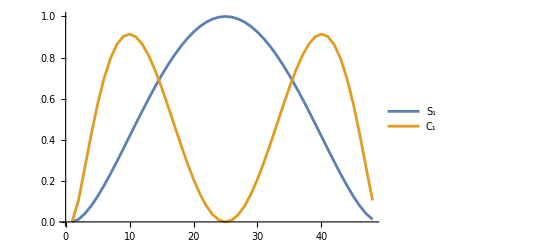

Note in the above plot that entanglement capacity is minimized when entanglement is maximized or when it is zero.

As with the case of entropy vectors, we can compile the entanglement capacity across all possible bipartitions of the Hilbert space for a given input state. Let us define this object as the Entanglement Capacity vector, which we can compute using the CapacityVectorBuilder[densityMatrix_] function.

```mathematica
CapacityVectorBuilder[GHZ3Dens]
CapacityVectorBuilder[sampleState]
```

{{0},{0},{0},{0},{0},{0},{0}}

{{0.0953456},{0.0325407},{0.10665},{0.668673},{0.259594},{0.297802},{1.16677}}

We can likewise evolve a system through a quantum circuit and observe the evolution of entanglement capacity across the circuit.

```mathematica
initalState= GenerateVacuumKet[3];
circuit = {HadamardGate[3,1],HadamardGate[3,2],HadamardGate[3,3],TGate[3,1],CNOTGate[3,{1,2}],TGate[3,2],CNOTGate[3,{2,3}],TGate[3,3],CNOTGate[3,{3,1}]};

state = initalState;
Table[state = circuit[[i]].state;
N[Flatten@CapacityVectorBuilder[DensityMatrix[state]]],{i,Length[circuit]}]
```

{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.808424+6.49483×10^-18 ⅈ,0.,0.808424,0.808424-3.51208×10^-17 ⅈ,0.,0.808424+6.49483×10^-18 ⅈ,0.}}

As we move from left to right in the above array, we observe the accumulation of non-local magic in the system.